## Initial Stuff

```mathematica
SetDirectory[NotebookDirectory[]];
filelist = FileNames[All,"../plinear2"];
filenum =1;
```

### Useful functions

```mathematica
kBinslin[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=(kmax-kmin)/(Nmax-1)//N;
result=Table[kmin +(i-1) Δ,{i,1,Nmax}];
result
];
```

```mathematica
(* Nmax log k bins, from kmin to kmax *)
kBins[Nmax_,kmin_,kmax_]:=Module[{Δ,result},
Δ=1/(Nmax-1)Log[kmax/kmin]//N;
result=Table[kmin Exp[(i-1) Δ],{i,1,Nmax}];
result
];
```

### Plotting parameters and simple loop kernels

```mathematica
NmaxPlot=100;
NmaxFit=100;
kminPlot= 10^-3;
kminFit= 10^-3;
kmaxPlot=2.;
kmaxFit=0.6;
knPlot=kBins[NmaxPlot,kminPlot,kmaxPlot];
knFit=kBins[NmaxFit,kminFit,kmaxFit];
knFitlin=kBinslin[NmaxPlot,kminPlot,kmaxFit];
```

```mathematica
F3[q_,kmq_]=85/1512+(5 k^2)/(168 kmq^2)+kmq^2/(72 k^2)-(31 k^4)/(1512 q^4)-k^6/(252 kmq^2 q^4)+(11 k^2 kmq^2)/(252 q^4)-(5 kmq^4)/(504 q^4)-kmq^6/(108 k^2 q^4)-(5 k^2)/(1512 q^2)-k^4/(504 kmq^2 q^2)-(13 kmq^2)/(1512 q^2)+kmq^4/(72 k^2 q^2)-(7 q^2)/(216 k^2)-(19 q^2)/(504 kmq^2)+q^4/(72 k^2 kmq^2);
F3int=F3[√(qvec.qvec),√(kminq.kminq)]/.{kminq->k{0,0,1}-q{0,√(1-ν^2),ν},qvec->q{0,√(1-ν^2),ν}}//Simplify;

F2[q2_,kminq2_]=5/14+3(k^2/(28q2))+3(k^2/(28kminq2))-5(q2/(28kminq2))-5(kminq2/(28q2))+k^4/(14kminq2 q2);
F2int=F2[qvec.qvec,kminq.kminq]/.{kminq->k{0,0,1}-q{0,√(1-ν^2),ν},qvec->q{0,√(1-ν^2),ν}}//Simplify;
```

```mathematica
(*F3intν[ν_]=Integrate[F3int,ν];*)
```

```mathematica
(*F3intνval=F3intν[1]-F3intν[-1]//FullSimplify*)
```

```mathematica
(*F3intUVν=Normal[Series[F3intνval,{q,∞,2}]]*)
```

```mathematica
(*F3intUVsafe=F3intνval+(61 k^2)/(945 q^2)//Simplify;*)
```

### General Perturbation Theory Kernels

```mathematica
perm12=Permutations[{q1,q2}];
perm123=Permutations[{q1,q2,q3}];
perm1234=Permutations[{q1,q2,q3,q4}];
```

```mathematica
Clear[Fn,Gn,n,m,k1,k2,k3];
Fn[n_,v_]:=Fn[n,v]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))((2n+1)al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
Gn[n_,v_]:=Gn[n,v]=If[n==1,1,Sum[Gn[m,v[[1;;m]]]/((2n+3)(n-1))(3al[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Fn[n-m,v[[m+1;;n]]]+2n be[Total[v[[1;;m]]],Total[v[[m+1;;n]]]]Gn[n-m,v[[m+1;;n]]]),{m,1,n-1}]];
```

```mathematica
F2s[q1_,q2_]=Simplify[Sum[1/Length[perm12]Fn[2,{perm12[[i,1]],perm12[[i,2]]}],{i,1,Length[perm12]}]];
F3s[q1_,q2_,q3_]=Simplify[Sum[1/Length[perm123]Fn[3,{perm123[[i,1]],perm123[[i,2]],perm123[[i,3]]}],{i,1,Length[perm123]}]];
```

```mathematica
F4s[q1_,q2_,q3_,q4_]=Simplify[Sum[1/Length[perm1234]Fn[4,{perm1234[[i,1]],perm1234[[i,2]],perm1234[[i,3]],perm1234[[i,4]]}],{i,1,Length[perm1234]}]];
```

```mathematica
alf[k1_,k2_]=(k1+k2).k1/(k1.k1);
bef[k1_,k2_]=(k1+k2).(k1+k2)(k1.k2)/2/(k1.k1)/(k2.k2) ;
alfm[k1_,k2_]=1+1/2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)/mag[k1]^2;
befm[k1_,k2_]=(mag[k1+k2]^2(mag[k1+k2]^2-mag[k1]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2);
sigma2[k1_,k2_]=1/4((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)^2)/(mag[k1]^2 mag[k2]^2)-1;
```

```mathematica
Gal3[k1_,k2_,k3_]:=-1/2(1-3((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)^2)/(4 mag[k1]^2 mag[k2]^2)+ ((mag[k1+k2]^2-mag[k1]^2-mag[k2]^2)(mag[k1+k3]^2-mag[k1]^2-mag[k3]^2)(mag[k3+k2]^2-mag[k3]^2-mag[k2]^2))/(4 mag[k1]^2 mag[k2]^2 mag[k3]^2));
```

### Linear Power Spectrum (not IR re-summed)

```mathematica
plindat=(*ImportString[StringReplace[Import[(*filelist⟦58⟧*)filelist⟦1⟧,"Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];*)Import["../patchy_pk.dat"];
kmin=plindat⟦1,1⟧;
kmax=Last[plindat]⟦1⟧;
```

```mathematica
As=plindat⟦1,2⟧;
kb=plindat⟦1,1⟧;
(*pextra=Table[{10^(-10+( i-1) 0.2), As (10^(-10+ (i-1) 0.2)/kb)^0.965},{i,1,30}];*)
```

```mathematica
(*plindat2=Join[pextra,plindat];*)
```

```mathematica
Clear[Plin]
Plin=Interpolation[plindat];
```

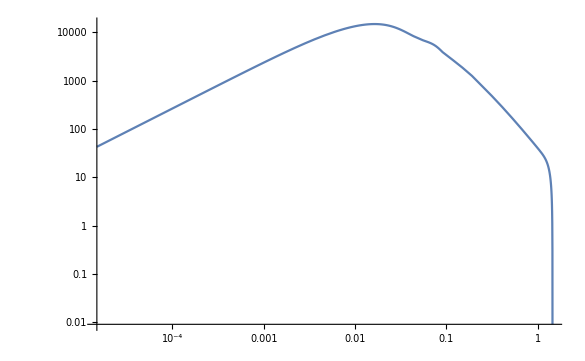

```mathematica
LogLogPlot[Plin[k],{k,kmin,3},PlotRange->Automatic]
```

### Linear Power Spectrum (IR re-summed)

#### Get non-re-summed power spectrum

```mathematica
SetDirectory[NotebookDirectory[]];
filelist = FileNames[All,"../plinear2"];
```

```mathematica
plindat=(*ImportString[StringReplace[Import[filelist⟦filenum⟧,"Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];*)Import["../patchy_pk.dat"];
Plin=Interpolation[plindat];
```

```mathematica
Plin["Domain"]
```

{{0.0000150000000000000004,1.}}

#### Obtain Eisenstein-Hu PS

```mathematica
GetCosmoParam[paramstring_]:=Module[{Ωb,Ωc,h,ns},
(*Obtain cosmological parameters from first line in power spectrum .dat, assuming that the paramstring is for example:{"Ob0.05","Oc0.20","h0.62","ns1.10.dat"};*)

Ωb =ToExpression[StringSplit[paramstring⟦1⟧,"b"]⟦2⟧];Ωc= ToExpression[StringSplit[paramstring⟦2⟧,"c"]⟦2⟧];h =ToExpression[ StringSplit[paramstring⟦3⟧,"h"]⟦1⟧];ns = ToExpression[StringSplit[StringSplit[paramstring⟦4⟧,"s"]⟦2⟧,".dat"]⟦1⟧];
{Ωb,Ωc,h,ns}
]
```

```mathematica
GetEHuPS[k_,z_,Ωb_,Ωc_,h_,ns_]:=Module[{Ωm,logAs,Ho,ΩL,As,σ8,Tcmb,alph,ss,gamma,q,L0,C0,Tnw,Dlin,Dlinz,kP,PLnw},
(*Function that Outputs the E-Hu power spectrum pEH[k,z] for one cosmology;
Inputs:          ;
- k: scale;
- z: redshift;
- Ωb: baryon density parameter at z=0;
- Ωc: CDM density parameter at z=0;
- h: H0/(100 km/s/Mpc);
- ns: standard ns parameter;

Assumptions: flat universe, logAs=3.04, Tcmb=2.728;
*)

Ωm=Ωb+Ωc;ΩL=1-Ωm;

logAs = 3.091;Ho=1/2998 ;
As=(*2.21 10^-9*)10^-10 Exp[logAs];
σ8=0.8;Tcmb=2.728;
alph=1-0.328 Log[431 Ωm h^2] Ωb/Ωm+0.38 Log[22.3  Ωm h^2](Ωb/Ωm)^2;
ss=44.5 Log[9.83/(Ωm h^2)]/(√(1+10(Ωb h^2)^0.75))h;
gamma=Ωm h (alph+(1-alph)/(1+(0.43 ss k)^4));
q= (Tcmb/2.7)^2 k/gamma;
L0=Log[2 ⅇ+1.8 q];
C0=14.2+731/(1+62.5 q);
Tnw=L0/(L0+C0 q^2);
        Dlin[a_]:=-a/(3 √(Ωm (a^3 ΩL+Ωm))) (-8 Ωm Hypergeometric2F1[-1/2,5/6,11/6,-(a^3 ΩL)/Ωm]+(2 a^3 ΩL+5 Ωm) Hypergeometric2F1[1/2,5/6,11/6,-(a^3 ΩL)/Ωm]);
Dlinz=Dlin[1/(1+z)];
kP=0.05 h^-1;
2 π^2 4/25 (As k)/(Ho^4 Ωm^2)Dlinz^2(k/kP)^(ns-1)Tnw^2
]
```

```mathematica
paramstring = StringSplit[filelist⟦filenum⟧,"_"]⟦2;;⟧;
```

```mathematica
(*{Ωbo,Ωco,h,ns}=GetCosmoParam[paramstring];*)
Ωbo = 0.0220453;
Ωco = 0.119;
h = 0.6777;
ns = 0.96;
```

```mathematica
PLnw[k_,z_]=GetEHuPS[k,z,Ωbo,Ωco,h,ns];
```

```mathematica
pEH=Table[{plindat⟦i,1⟧,PLnw[plindat⟦i,1⟧,0.57]},{i,1,Length[plindat]}];
```

```mathematica
(*ListLogLinearPlot[Transpose@{klin,plindat⟦All,2⟧/pEH⟦All,2⟧},Joined->True,PlotRange->{All,{0.935,1.065}},Frame->True,GridLines->{{}, {0.94,1.,1.06}}]*)
```

#### Smooth ratio and then multiply by the EH spectrum

```mathematica
Clear[f];
f[iR_,k_,λ_]:=NIntegrate[iR[10^x] PDF[NormalDistribution[Log10[k],λ]][x],{x,Log10[k]-4 λ,Log10[k]+4 λ},WorkingPrecision->10]
```

```mathematica
ExtractWiggle[plindat_,psmoothdat_]:=Module[{iR,λ,pnw,pw,ipnw,ipw,ktab},
λ=0.25;

ktab=plindat⟦All,1⟧;
iR=Interpolation[Transpose@{ktab,plindat⟦All,2⟧/psmoothdat⟦All,2⟧}];

pnw=Table[{ktab⟦i⟧,psmoothdat⟦i,2⟧ f[iR,ktab⟦i⟧,λ]},{i,1,Length[ktab]}];
pw=Table[{ktab⟦i⟧,plindat⟦i,2⟧-pnw⟦i,2⟧},{i,1,Length[ktab]}];
ipnw=Interpolation[pnw];
ipw=Interpolation[pw];

{ipnw,ipw}
]
```

```mathematica
GetΣtot2[psmooth_,f_]:=Module[{Σ2,δΣ2,Σtot2,losc=110,kmin},
kmin=psmooth["Domain"]⟦1,1⟧;
Σ2=1/(6 π^2)NIntegrate[(1-SphericalBesselJ[0,q losc]+2 SphericalBesselJ[2,q losc])psmooth[q],{q,kmin,0.2}];δΣ2=1/(2 π^2)NIntegrate[SphericalBesselJ[2,q losc]psmooth[q],{q,kmin,0.2}];Σtot2=(1+f 1/3(2+f))Σ2+f^2(-2/15)δΣ2
]
ResumPSNLO[k_,psmooth_,pwiggle_,Σtot2_]:=psmooth[k]+(1+k^2 Σtot2) Exp[-k^2 Σtot2]pwiggle[k] (*Next to leading order resummation*);
ResumPSLO[k_,psmooth_,pwiggle_,Σtot2_]:=psmooth[k]+ Exp[-k^2 Σtot2]pwiggle[k] (*Leading order resummation*);
```

```mathematica
{ipnw,ipw}=ExtractWiggle[plindat,pEH];
```

```mathematica
Σtot2=GetΣtot2[ipnw,0.7770083924901465];
```

```mathematica
presLO[k_,f_]:=ResumPSLO[k,ipnw,ipw,Σtot2];
presNLO[k_,f_]:=ResumPSNLO[k,ipnw,ipw,Σtot2];
```

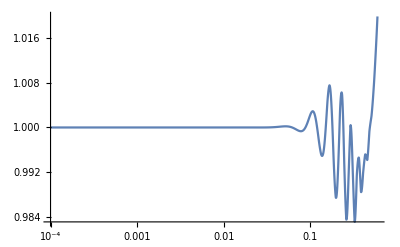

```mathematica
LogLinearPlot[presNLO[k,0.7770083924901465]/Plin[k],{k,0.0001,0.6},PlotRange->All]
```

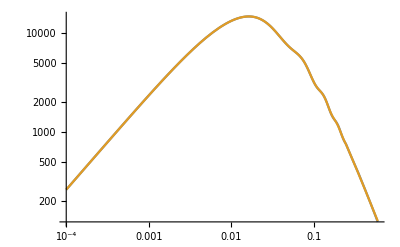

```mathematica
LogLogPlot[{Plin[q],presNLO[q,0.7770083924901465]},{q,0.0001,0.6}]
```

## Fit broadband power spectrum

```mathematica
imax=3;
```

### Fit integer powers to linear power spectrum - linear fit with fixed parameters

```mathematica
Pirres[k_]=presNLO[k,0.7770083924901465];
(*Plin[k_]=presNLO[k,0.6];*)

fitparams={};
```

```mathematica
GetFitFunctions[imax_]:=Module[{kuv1,kuv2,kuv3,kuv4,kpeak1,kpeak2,kpeak3,kpeak4},

kuv1=0.06767125673321318;
kuv2=0.0012067559385398187;
kuv3=0.013962410148102322;
kuv4=0.00003617351522205301;
kpeak1=-0.010897520818797794;
kpeak2=-0.0011758078803276375;
kpeak3=-0.002544972487161462;
kpeak4=-0.00001841386126698319;
Flatten[Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),(k/(1/20))^4/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]]];


IntegerFit[Pirres_,knFit_]:=Module[{MyPsmoothtab,errors,imax=5,kuv1,kuv2,kuv3,kuv4,kpeak1,kpeak2,kpeak3,kpeak4},
MyPsmoothtab = Table[{knFit⟦i⟧,Pirres[knFit⟦i⟧]},{i,1,Length[knFit]}];
errors=Flatten[Table[{MyPsmoothtab⟦i,2⟧ 10^-6},{i,1,Length[knFit]}]];
MyFitFunctions=GetFitFunctions[imax];

nlm=LinearModelFit[MyPsmoothtab,MyFitFunctions,k,Weights->1/errors^2,IncludeConstantBasis->False]; 
Pinteger[k_]=nlm[k]/k^ibias;
Print[LogLogPlot[{Abs[Pinteger[k]/Plin[k]-1],Abs[Plin[k]/Pinteger[k]-1],0.1,0.005,0.01,0.02,0.05},{k,0.001,2.},PlotRange-> All,PlotLabel->"imax="<>ToString[imax]]];
Print[LogLogPlot[{Pinteger[k],Plin[k]},{k,0.001,3},PlotRange->All]];
MyPWiggle[k_]=Plin[k]-Pinteger[k];
nlm["BestFitParameters"]
]
```

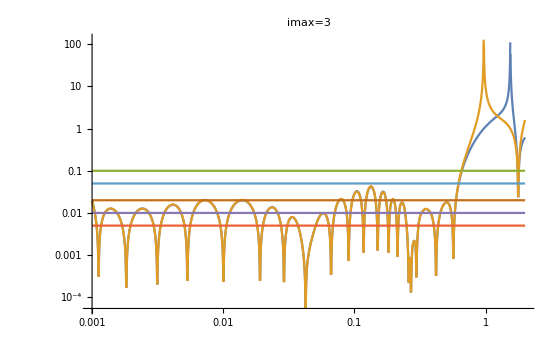

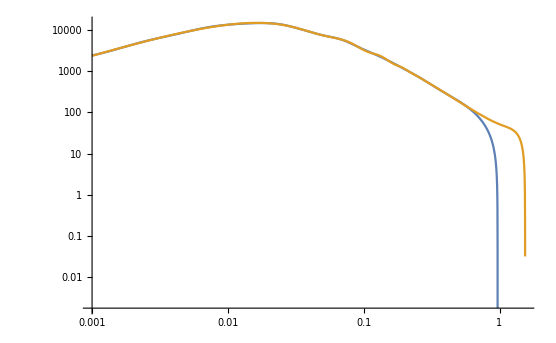

{-113.753,4618.77,114185.,-72928.6,-3707.43,-360.081,-274891.,306214.,5582.13,-62.1672,299549.,-691166.,-10813.1,11089.,-119982.,508210.}

```mathematica
ibias=0;
Clear[kuv,parametersconstraint,Psmoothtab,MyPsmoothtab,errors,kuv1,kuv2,kuv3,nlm,MyFitFunctions,Pinteger];
Psmoothtab = Table[{knFit⟦i⟧,Pirres[knFit⟦i⟧]},{i,1,Length[knFit]}];
MyPsmoothtab=Table[{Psmoothtab⟦i,1⟧,Psmoothtab⟦i,1⟧^ibias Psmoothtab⟦i,2⟧},{i,1,Length[knFit]}];
errors=Flatten[Table[{Psmoothtab⟦i,1⟧^ibias Psmoothtab⟦i,2⟧ 10^-6},{i,1,Length[knFit]}]];

imax=3;

ClearAll[kuv1,kuv2,kuv3,kpeak1,kpeak2,kpeak3,nlm,Pinteger]

(*Henry new params;*)

kuv1=0.069;
kuv2=0.0082;
kuv3=0.0013;
kuv4=0.0000135;
kpeak1=-0.034;
kpeak2=(*0.006*)-0.001;
kpeak3=(*0.000076*)-0.000076;
kpeak4=-0.0000156;


Parameters=Flatten[Table[{a1[i],a2[i],a3[i],a4[i]},{i,0,imax}]];
MyFitFunctions=Flatten[Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]];
nlm=LinearModelFit[MyPsmoothtab,MyFitFunctions,k,Weights->1/errors^2,IncludeConstantBasis->False]; 
Pinteger[k_]=nlm[k]/k^ibias;
(*Pintegerinterp=FunctionInterpolation[Pinteger[k],{k,0.0001,10}];*)
LogLogPlot[{Abs[Pinteger[k]/Pirres[k]-1],Abs[Pirres[k]/Pinteger[k]-1],0.1,0.005,0.01,0.02,0.05},{k,0.001,2.},PlotRange-> All,PlotLabel->"imax="<>ToString[imax]]
LogLogPlot[{Pinteger[k],Pirres[k]},{k,0.001,3},PlotRange->All]
MyPWiggle[k_]=Pirres[k]-Pinteger[k];
coefnowig=N[nlm["BestFitParameters"],50]
```

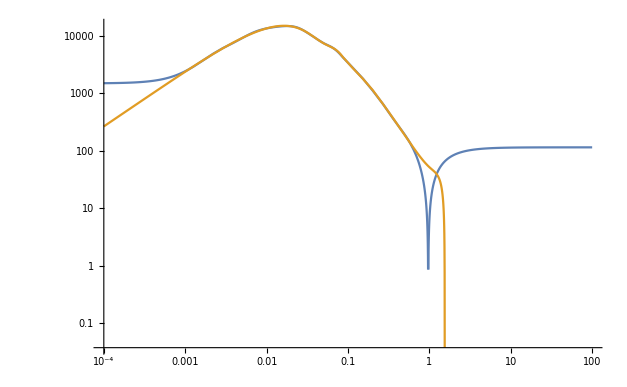

```mathematica
LogLogPlot[{Evaluate@Abs@{Pinteger[k]},Pirres[k]},{k,0.0001,100},PlotRange->All]
```

## Fit wiggles

### Tabulate wiggle data for fitting

```mathematica
(*LogLinearPlot[{MyPWiggle[k]},{k,0.001,2.},PlotRange-> All]*)
```

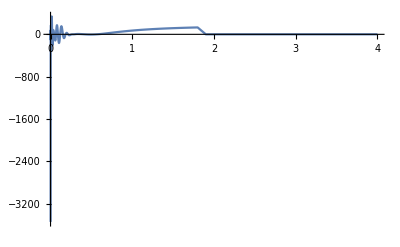

```mathematica
Clear[data1,errors1,dataWiggle,errorsWiggle]
kmin=1/1000;
kmaxwiggle=1.8;
kmaxhigh=4.0;
Nlinearmaxtemp=300;
knwig=kBins[Nlinearmaxtemp,kmin,kmaxwiggle];
kextra=Table[kmaxwiggle+0.1 i,{i,1,Round[(kmaxhigh-kmaxwiggle)/0.1]}];
dataWiggle=Join[Table[{knwig⟦i⟧,MyPWiggle[knwig⟦i⟧]},{i,1,Nlinearmaxtemp}],Table[{kmaxwiggle+0.1 i,0},{i,1,Round[(kmaxhigh-kmaxwiggle)/0.1]}]];
Nlinearmax=Nlinearmaxtemp+Round[(kmaxhigh-kmaxwiggle)/0.1];
PWiggleIinter=Interpolation[dataWiggle,Method->"Hermite",InterpolationOrder->3];
Show[ListLinePlot[{dataWiggle},PlotRange->All]]
```

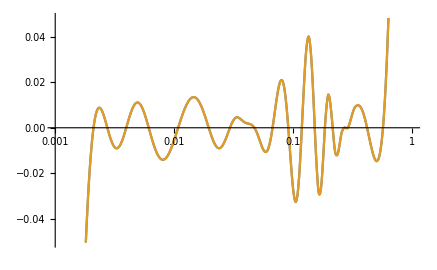

```mathematica
LogLinearPlot[{MyPWiggle[k]/Plin[k],PWiggleIinter[k]/Plin[k]},{k,0.001,1}]
```

### BW Fit

#### Overall fit

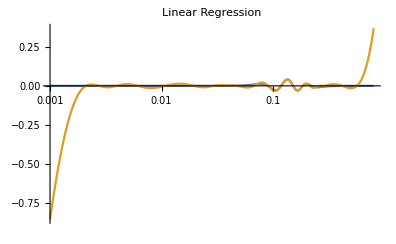

```mathematica
dataWigglelow= Select[dataWiggle,#⟦1⟧<6&];
ibiasW=1;
MyPwiggletab=Table[{dataWigglelow⟦i,1⟧,dataWigglelow⟦i,1⟧^ibiasW dataWigglelow⟦i,2⟧},{i,1,Length[dataWigglelow]}];
imax=(*20*)7;
kmaxBW=(*0.35*)0.242;
kminBW=0.09;
m0[i_]=0.74kminBW ⅇ^(Log[kmaxBW/kminBW] (1.1i)/imax);
δBW[i_]=0.06 ⅇ^(Log[kmaxBW/kminBW] 0.88i/imax);
Massfunction[i_]:=ρ[i] k^(2+ibiasW)(1/((k^2-m0[i]^2)^2+m0[i]^2 δBW[i]^2))^2;

fitTab = Table[Massfunction[i]/.k->MyPwiggletab⟦j,1⟧/.{ρ[i_]->1},{j,1,Length[MyPwiggletab]},{i,1,imax}];
vals = Inverse[(Transpose[fitTab].fitTab)].Transpose[fitTab].MyPwiggletab⟦All,2⟧;
func[k_] =Sum[Massfunction[i]vals⟦i⟧/.{ρ[i_]->1},{i,1,imax}]/k^ibiasW;
LogLinearPlot[{func[k]/Plin[k],PWiggleIinter[k]/Plin[k]},{k,0.001,0.8},PlotRange->All,PlotLabel->"Linear Regression"]
(*LogLinearPlot[{PwiggleFitlow[k]/Plin[k],PWiggleIinter[k]/Plin[k]},{k,0.001,2  },PlotRange->All,PlotLabel->"Linearmodelfit"]*)
```

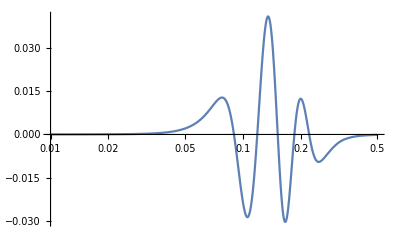

```mathematica
LogLinearPlot[func[k]/Plin[k],{k,0.01,0.5},PlotRange->All]
```

#### Fine-grained Fit from 0.3 to 1.0

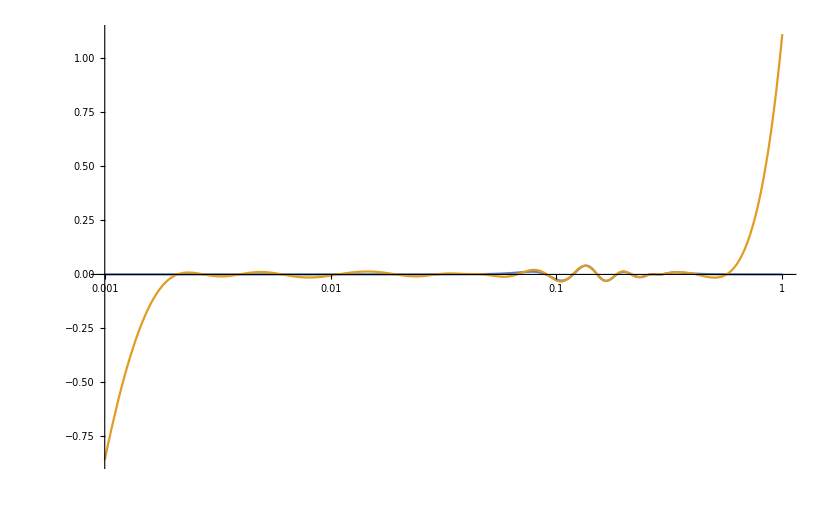

```mathematica
dataWigglehigh=Select[Table[{dataWiggle⟦i,1⟧,dataWiggle⟦i,2⟧-func[dataWiggle⟦i,1⟧]},{i,1,Length[dataWiggle]}],#⟦1⟧<1&];
ibiasW=1;
MyPwiggletab=Table[{dataWigglehigh⟦i,1⟧,dataWigglehigh⟦i,1⟧^ibiasW dataWigglehigh⟦i,2⟧},{i,1,Length[dataWigglehigh]}];
imax=4;
kmaxBW=0.5;
kminBW=0.21;
m0high[i_]=1.08kminBW ⅇ^(Log[kmaxBW/kminBW] (0.2i)/imax);
δBWhigh[i_]=0.017 ⅇ^(i/imax);
Massfunction[i_]:=ρ[i] k^(2+ibiasW)(δBWhigh[i]/((k^2-m0high[i]^2)^2+δBWhigh[i]^2))^2;
fitTab = Table[Massfunction[i]/.k->MyPwiggletab⟦j,1⟧/.{ρ[i_]->1},{j,1,Length[MyPwiggletab]},{i,1,imax}];
valshigh = Inverse[(Transpose[fitTab].fitTab)].Transpose[fitTab].MyPwiggletab⟦All,2⟧;
funchigh[k_] =Sum[Massfunction[i]valshigh⟦i⟧/.{ρ[i_]->1},{i,1,imax}]/k^ibiasW;
LogLinearPlot[{(func[k]+funchigh[k])/Plin[k],PWiggleIinter[k]/Plin[k]},{k,0.001,1  },PlotRange->All]
```

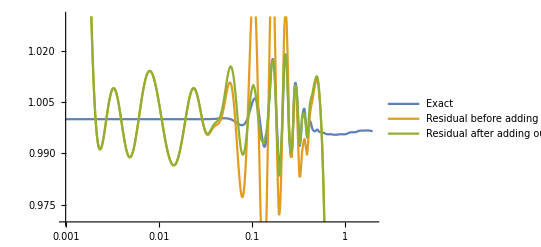

```mathematica
LogLinearPlot[{(Pinteger[k]+MyPWiggle[k])/Plin[k],Pinteger[k]/Plin[k],(Pinteger[k]+func[k]+funchigh[k])/Plin[k]},{k,0.001,2},PlotRange-> {0.97,1.03},PlotLegends->{"Exact","Residual before adding our fit to Pwiggle","Residual after adding our fit to Pwiggle"}]
```

## Numerical check P13 and P22

Turn this on/off if you are fitting Plin directly, otherwise keep it commented.

```mathematica
PSexact[k_]=Pirres[k];
Psmoothfit[k_]=Pinteger[k];
(*Pwigglefit[k_]=func[k]+funchigh[k];
Pwigglefitfew[k_]=func[k];*)
Pfit[k_]=Pinteger[k];(*+Pwigglefit[k];*)
```

```mathematica
qir=0.001; quv=2;
P13mioExact[kk_]:=(6/(2π)^2)PSexact[kk](NIntegrate[q^2(F3int+ (61 kk^2)/(2 945 q^2)) PSexact[q]/.{k->kk},{q,qir,quv},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->4]);
P22mioExact[kk_]:=(2/(2π)^2)(NIntegrate[q^2 F2int^2 PSexact[q]PSexact[√(q^2+kk^2-2 kk q ν)]Boole[√(q^2+kk^2-2 kk q ν)> qir]/.{k->kk},{q,qir,quv},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->4]);


P13mioFullFit[kk_]:=(6/(2π)^2)PSexact[kk](NIntegrate[q^2(F3int+(61 kk^2)/(2 945 q^2)) Pfit[q]/.{k->kk},{q,qir,quv},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->4]);
P13mioSmoothFit[kk_]:=(6/(2π)^2)PSexact[kk](NIntegrate[q^2(F3int+(61 kk^2)/(2 945 q^2)) Psmoothfit[q]/.{k->kk},{q,qir,quv},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->4]);
(*P13mioWiggleFit[kk_]:=(6/(2π)^2)PSexact[kk](NIntegrate[q^2(F3int+(61 kk^2)/(2 945 q^2)) Pwigglefit[q]/.{k->kk},{q,qir,quv},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->4]);*)


P22mioFullFit[kk_]:=(2/(2π)^2)(NIntegrate[q^2 F2int^2 Pfit[q]Pfit[√(q^2+kk^2-2 kk q ν)]Boole[√(q^2+kk^2-2 kk q ν)> qir]/.{k->kk},{q,qir,quv},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->4]);

P22mioSmoothFit[kk_]:=(2/(2π)^2)(NIntegrate[q^2 F2int^2 Psmoothfit[q]Psmoothfit[√(q^2+kk^2-2 kk q ν)]Boole[√(q^2+kk^2-2 kk q ν)> qir]/.{k->kk},{q,qir,quv},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->4]);
(*P22mioWiggleSmoothFit[kk_]:=(2/(2π)^2)2(NIntegrate[q^2 F2int^2 Pwigglefit[q]Psmoothfit[√(q^2+kk^2-2 kk q ν)]Boole[√(q^2+kk^2-2 kk q ν)> qir]/.{k->kk},{q,qir,quv},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->4]);
P22mioWiggleWiggleFewFit[kk_]:=(2/(2π)^2)2(NIntegrate[q^2 F2int^2 Pwigglefitfew[q]Pwigglefitfew[√(q^2+kk^2-2 kk q ν)]Boole[√(q^2+kk^2-2 kk q ν)> qir]/.{k->kk},{q,qir,quv},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->4]);*)



ΔP13mio[kk_]:=(6/(2π)^2)PSexact[kk](NIntegrate[q^2(F3int+(61 kk^2)/(2 945 q^2)) (Pfit[q]-PSexact[q])/.{k->kk},{q,qir,quv},{ν,-1,1},AccuracyGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]);

ΔP22mio[kk_]:=(2/(2π)^2)(NIntegrate[q^2 F2int^2(Pfit[q]Pfit[√(q^2+kk^2-2 kk q ν)] -PSexact[q]PSexact[√(q^2+kk^2-2 kk q ν)])Boole[√(q^2+kk^2-2 kk q ν)> qir]/.{k->kk},{q,qir,quv},{ν,-1,1},AccuracyGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]);
(*ΔP22miowigglefew[kk_]:=(2/(2π)^2)(NIntegrate[q^2 F2int^2((Psmoothfit[q]Psmoothfit[√(q^2+kk^2-2 kk q ν)]+2 Pwigglefitfew[q]Psmoothfit[√(q^2+kk^2-2 kk q ν)]+Pwigglefitfew[q]Pwigglefitfew[√(q^2+kk^2-2 kk q ν)])-PSexact[q]PSexact[√(q^2+kk^2-2 kk q ν)])Boole[√(q^2+kk^2-2 kk q ν)> qir]/.{k->kk},{q,qir,quv},{ν,-1,1},AccuracyGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]);*)


P1loopExact[kk_]:=P13mioExact[kk]+P22mioExact[kk];
P1loopFullFit[kk_]:=P13mioFullFit[kk]+P22mioFullFit[kk];

ΔP1loopFullFit[kk_]:=ΔP13mio[kk]+ΔP22mio[kk];

(*ΔP1loopWiggleFew[kk_]:=ΔP13mio[kk]+ΔP22miowigglefew[kk];*)

(*kprova=0.1;
P13mioExact[kprova]//AbsoluteTiming
P22mioExact[kprova]//AbsoluteTiming
P1loopExact[kprova]//AbsoluteTiming
P13mioFullFit[kprova]//AbsoluteTiming
P22mioFullFit[kprova]//AbsoluteTiming
P1loopFullFit[kprova]//AbsoluteTiming
(P1loopExact[kprova]/P1loopFullFit[kprova])-1//AbsoluteTiming*)
```

```mathematica
ΔP1loopFullFitTab=Table[Print[kprova];{kprova,ΔP1loopFullFit[kprova]},{kprova,{0.01,0.05,0.1,0.2,0.3,0.4}}];

(*ΔP1loopWiggleFewTab=Table[{kprova,ΔP1loopWiggleFew[kprova]},{kprova,{0.01,0.05,0.1,0.2,0.3,0.4}}];*)
```

0.01

0.05

0.1

0.2

0.3

0.4

```mathematica
(*P1loopIntegerTab=Table[{kprova,P1loopInteger[kprova]},{kprova,{0.01,0.05,0.1,0.2,0.3,0.4}}];*)
P1loopExactTab=Table[{kprova,P1loopExact[kprova]},{kprova,{0.01,0.05,0.1,0.2,0.3,0.4}}];
```

```mathematica
kprovaTab ={0.01,0.05,0.1,0.2,0.3,0.4};

Table[{kprovaTab⟦i⟧,ΔP1loopFullFitTab⟦i,2⟧/P1loopExactTab⟦i,2⟧,ΔP1loopFullFitTab⟦i,2⟧/Plin[kprovaTab⟦i⟧]},{i,1,Length[kprovaTab]}]
(*Table[{kprovaTab⟦i⟧,ΔP1loopWiggleFewTab⟦i,2⟧/P1loopExactTab⟦i,2⟧,ΔP1loopWiggleFewTab⟦i,2⟧/Plin[kprovaTab⟦i⟧]},{i,1,Length[kprovaTab]}]*)
```

{{0.01,0.000406759,7.0882×10^-8},{0.05,0.000864764,0.0000261144},{0.1,-0.00140697,-0.000263323},{0.2,-0.00951958,-0.00713248},{0.3,0.00567281,0.0102864},{0.4,-0.00753373,-0.0236075}}

## Numerical check of bispectrum

### Numerical integration bounds

```mathematica
qir=0.0001; quv=1;
```

```mathematica
Clear[k1vec,k2vec,qvec,k1,k2,k3,ϕs,q]
k1vec=k1{0,0,1};
ν2= (k3^2-k2^2-k1^2)/(2k1 k2);
k2vec=k2{0,√(1-ν2^2),ν2};
k3vec=-k1vec-k2vec;

qvec=q{Cos[ϕs] √(1-ν^2),Sin[ϕs] √(1-ν^2),ν};
k1mqvec=k1vec-qvec//Simplify;
k2pqvec=k2vec+qvec//Simplify;
k1pqvec=k1vec+qvec//Simplify;
k2mqvec=k2vec-qvec//Simplify;
k3pqvec=k3vec+qvec//Simplify;
k3mqvec=k3vec-qvec//Simplify;
```

```mathematica
subs={k1mq->√(k1mqvec.k1mqvec),k2pq->√(k2pqvec.k2pqvec),k1pq->√(k1pqvec.k1pqvec),k2mq->√(k2mqvec.k2mqvec),k3pq-> (k3pqvec.k3pqvec)^(1/2),k3mq-> (k3mqvec.k3mqvec)^(1/2)}//Simplify;
subsp1loop={kmq-> √(q^2+k^2-2 k q ν),kpq-> √(q^2+k^2+2 k q ν)};
```

```mathematica
magreps ={mag[0]-> 0,mag[-q]->q,mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k3]->k3,mag[-k1]->k1,mag[-k2]->k2,mag[-k1-k2]->k3,mag[k1+k2]->k3,mag[-k1+q]->k1mq,mag[k1-q]->k1mq,mag[-k1-q]->k1pq,mag[k1+q]->k1pq,mag[-k2+q]->k2mq,mag[k2-q]->k2mq,mag[-k2-q]->k2pq,mag[k2+q]->k2pq,mag[-k1-k2-q]->k3mq,mag[k1+k2+q]->k3mq,mag[-k1-k2+q]->k3pq,mag[k1+k2-q]->k3pq,mag[-k3]->k3,mag[-k1-k3]->k2,mag[k1+k3]->k2,mag[-k3+q]->k3mq,mag[k3-q]->k3mq,mag[-k3-q]->k3pq,mag[k3+q]->k3pq,mag[-k1-k3-q]->k2mq,mag[k1+k3+q]->k2mq,mag[-k1-k3+q]->k2pq,mag[k1+k3-q]->k2pq,mag[-k2-k3]->k1,mag[k2+k3]->k1,mag[-k2-k3-q]->k1mq,mag[k2+k3+q]->k1mq,mag[-k2-k3+q]->k1pq,mag[k2+k3-q]->k1pq};
```

### B Tree Level

```mathematica
Clear[kerTree,Btree,Btreetot]
kerTree[k1_,k2_,k3_]=2 F2s[k1,k2]/.{al->alfm,be->befm}/.magreps//Simplify;
Btree[k1_,k2_,k3_]=10^-6 kerTree[k1,k2,k3]Plin[k1]Plin[k2];
kperms=NestList[RotateLeft,{k1,k2,k3},2];
Btreetot[k1_,k2_,k3_]=Total[Btree@@@kperms];
```

### B222

```mathematica
Clear[k1,k2,k3,q,b222ker,B222Exact,ΔB222]
```

```mathematica
ker222[k1_,k2_,k3_]=((((8F2s[q,-q+k1]F2s[-q+k1,q+k2]F2s[k2+q,-q]/.{al->alfm,be->befm})/.mag[-q]->mag[q])/.{mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k1+k2]->k3,mag[k1-q]->k1mq,mag[k2+q]->k2pq})//Simplify)/.subs;
```

```mathematica
B222Exact[k1sub_,k2sub_,k3sub_]:=Module[{ker222int,k1mqarg,k2pqarg},
ker222int=Simplify[ker222[k1sub,k2sub,k3sub],Assumptions->{q>0,-1<ν<1,0<ϕs<2π}];

k1mqarg=k1mq/.subs/.{k1-> k1sub, k2->k2sub, k3-> k3sub}//Simplify;
k2pqarg=k2pq/.subs/.{k1-> k1sub, k2->k2sub, k3-> k3sub}//Simplify;

1/(π)^(3/2)10^-6(NIntegrate[(q^2 ker222int(Pirres[q]Pirres[k1mqarg]Pirres[k2pqarg])),{q,qir,quv},{ν,-1,1},{ϕs,0,2π},WorkingPrecision->10,Method->{Automatic,"SymbolicProcessing"->0}])];
B222Integer[k1sub_,k2sub_,k3sub_]:=Module[{ker222int,k1mqarg,k2pqarg},
ker222int=Simplify[ker222[k1sub,k2sub,k3sub],Assumptions->{q>0,-1<ν<1,0<ϕs<2π}];

k1mqarg=k1mq/.subs/.{k1-> k1sub, k2->k2sub, k3-> k3sub}//Simplify;
k2pqarg=k2pq/.subs/.{k1-> k1sub, k2->k2sub, k3-> k3sub}//Simplify;

1/(π)^(3/2)10^-6(NIntegrate[(q^2 ker222int(Pinteger[q]Pinteger[k1mqarg]Pinteger[k2pqarg])),{q,qir,quv},{ν,-1,1},{ϕs,0,2π},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}])]
```

### B3211

```mathematica
Clear[ker3211,ker3211part2,ker3211part3,ker3211part4,ker3211part5,ker3211part6]
```

```mathematica
ker3211[k1_,k2_,k3_]=(((6F3s[-q,q-k2,-k1]F2s[q,k2-q]/.{al->alfm,be->befm})/.{mag[0]->0,mag[-q]->mag[q],mag[-k1]->mag[k1],mag[-k2]->mag[k2]})/.{mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k1+k2]->k3,mag[-k1-k2]->k3,mag[k1-q]->k1mq,mag[-k1+q]->k1mq,mag[k1+q]->k1pq,mag[-k1-q]->k1pq,mag[k2-q]->k2mq,mag[-k2+q]->k2mq,mag[k2+q]->k2pq,mag[k1+k2+q]->k3mq,mag[k1+k2-q]->k3pq,mag[-k1-k2+q]->k3pq}//Simplify)/.subs;
```

```mathematica
B3211Exact[k1sub_,k2sub_,k3sub_]:=Module[{ker3211int,k2mqarg},
ker3211int=Simplify[ker3211[k1sub,k2sub,k3sub],Assumptions->{q>0,-1<ν<1,0<ϕs<2π}];

k2mqarg=k2mq/.subs/.{k1-> k1sub, k2->k2sub, k3-> k3sub}//Simplify;

1/(π)^(3/2)10^-6 Plin[k1sub](NIntegrate[(q^2 ker3211int(Pirres[q]Pirres[k2mqarg])),{q,qir,quv},{ν,-1,1},{ϕs,0,2π},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}])];
B3211Integer[k1sub_,k2sub_,k3sub_]:=Module[{ker3211int,k2mqarg},
ker3211int=Simplify[ker3211[k1sub,k2sub,k3sub],Assumptions->{q>0,-1<ν<1,0<ϕs<2π}];

k2mqarg=k2mq/.subs/.{k1-> k1sub, k2->k2sub, k3-> k3sub}//Simplify;

1/(π)^(3/2)10^-6 Plin[k1sub](NIntegrate[(q^2 ker3211int(Pinteger[q]Pinteger[k2mqarg])),{q,qir,quv},{ν,-1,1},{ϕs,0,2π},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}])];
```

```mathematica
B3211Exacttot[k1_,k2_,k3_]:=B3211Exact[k1,k2,k3]+B3211Exact[k1,k3,k2]+B3211Exact[k2,k1,k3]+B3211Exact[k2,k3,k1]+B3211Exact[k3,k2,k1]+B3211Exact[k3,k1,k2];
```

```mathematica
B3211Integertot[k1_,k2_,k3_]:=B3211Integer[k1,k2,k3]+B3211Integer[k1,k3,k2]+B3211Integer[k2,k1,k3]+B3211Integer[k2,k3,k1]+B3211Integer[k3,k2,k1]+B3211Integer[k3,k1,k2];
```

### B3212

```mathematica
Clear[B3212,ker3212part1,ker3212part2,ker3212part3,ker13,ker13UV,ker13UVsafe]
```

```mathematica
ker13[k_]= (6F3s[q,-q,k]/.{al->alfm,be->befm}/.mag[-q]->mag[q]/.{mag[q]->q,mag[k]->k,mag[-k]->k,mag[k1+k2]->k3,mag[k-q]->kmq,mag[k+q]->kpq,mag[0]->0}/.subsp1loop//Simplify);
(*ker13diogoUVν=Normal[Series[ker13diogo/.subsp1loop,{q,∞,2}]];
ker13diogoUV=Integrate[ker13diogoUVν,{ν,-1,1}]/2;*)
(*ker13UV[k_]=-(61 k^2)/(315 q^2);
ker13UVsafe[k_]=ker13[k]-ker13UV[k]//Simplify;*)
(*intνker13[k_]=Integrate[ker13UVsafe[k],{ν,-1,1},Assumptions->{q>0,k>0}]*)
intνker13[k_]=1/(2520 k^3 q^5)(4 k q (30 k^6-151 k^4 q^2+250 k^2 q^4-105 q^6)+15 (k^2-q^2)^3 (2 k^2+7 q^2) (Log[(k-q)^2]-2 Log[k+q]));
ker3212[k1_,k2_,k3_] = F2s[k1,k2]/.{al->alfm,be->befm}/.magreps//Simplify;
```

```mathematica
P13Exact[ksub_]:=Module[{ker13int},
ker13int=intνker13[ksub];
1/(π)^(3/2)(2π)Plin[ksub]NIntegrate[q^2 ker13int Pirres[q],{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];

B3212Exact[k1sub_,k2sub_,k3sub_]:=10^-6 ker3212[k1sub,k2sub,k3sub]Plin[k1sub]P13Exact[k2sub];


P13Integer[ksub_]:=Module[{ker13int},
ker13int=intνker13[ksub];
1/(π)^(3/2)(2π)Plin[ksub]NIntegrate[q^2 ker13int Pinteger[q],{q,qir,quv},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];

B3212Integer[k1sub_,k2sub_,k3sub_]:=10^-6 ker3212[k1sub,k2sub,k3sub]Plin[k1sub]P13Integer[k2sub];
```

```mathematica
B3212Exact[0.2,0.2,0.1]
B3212Integer[0.2,0.2,0.1]
```

-2.01283

-2.01614

```mathematica
B3212Exacttot[k1_,k2_,k3_] :=B3212Exact[k1,k2,k3]+ B3212Exact[k1,k3,k2]+B3212Exact[k2,k1,k3]+B3212Exact[k2,k3,k1]+B3212Exact[k3,k1,k2]+B3212Exact[k3,k2,k1];
B3212Integertot[k1_,k2_,k3_] :=B3212Integer[k1,k2,k3]+ B3212Integer[k1,k3,k2]+B3212Integer[k2,k1,k3]+B3212Integer[k2,k3,k1]+B3212Integer[k3,k1,k2]+B3212Integer[k3,k2,k1];
```

```mathematica
B3212Exacttot[0.2,0.2,0.1] 
B3212Exacttot[0.1,0.2,0.2] 
B3212Exacttot[0.2,0.1,0.2] 
B3212Integertot[0.1,0.2,0.2] 
B3212Integertot[0.1,0.2,0.2] 
B3212Integertot[0.2,0.1,0.2]
```

-100.809

-100.809

-100.809

-100.969

-100.969

-100.969

```mathematica
ΔB3212[k1_,k2_,k3_]:=B3212Exacttot[k1,k2,k3]-B3212Integertot[k1,k2,k3]
```

```mathematica
ΔB3212[0.1,0.1,0.1]/B3212Exacttot[0.1,0.1,0.1]
```

-0.00120462

### B411

```mathematica
Clear[B411part1,B411part2,B411part3,ker411,ker411UV]
```

```mathematica
ker411[k1_,k2_,k3_]=((12F4s[q,-q,k1,k2]/.{al->alfm,be->befm})/.{mag[0]->0,mag[-q]->mag[q]})/.{mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k1+k2]->k3,mag[k1-q]->k1mq,mag[k1+q]->k1pq,mag[k2-q]->k2mq,mag[k2+q]->k2pq,mag[k1+k2+q]->k3mq,mag[k1+k2-q]->k3pq}/.subs;
(*Find UV limit of kernel*)

(*ker411lim=Normal[Series[ker411[k1,k2,k3]/.subs,{q,∞,2}]];
ker411limsimp=Simplify[ker411lim,{q>0,-1<ν<1}];
intker411lim=Integrate[ker411limsimp,{ϕs,0,2π},{ν,-1,1}]
ker411UV=intker411lim/(4π)//Simplify;*)
ker411UV[k1_,k2_,k3_]=-1/(679140 k1^2 k2^2 q^2)(12024 (k1^2-k2^2)^2 (k1^2+k2^2)-2 (22259 k1^4-38342 k1^2 k2^2+22259 k2^4) k3^2+20085 (k1^2+k2^2) k3^4+12409 k3^6);

ker411UVsafe[k1_,k2_,k3_]=ker411[k1,k2,k3]-ker411UV[k1,k2,k3];
```

```mathematica
B411Exact[k1sub_,k2sub_,k3sub_]:=Module[{ker411int},
ker411int =Simplify[ker411UVsafe[k1sub,k2sub,k3sub],Assumptions->{q>0,-1<ν<1,0<ϕs<2π}];
 1/(π)^(3/2)10^-6 Plin[k1sub]Plin[k2sub]NIntegrate[q^2(ker411int)Pirres[q],{q,qir,quv},{ν,-1,1},{ϕs,0,2π},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]]
```

```mathematica
B411Integer[k1sub_,k2sub_,k3sub_]:=Module[{ker411int},
ker411int =Simplify[ker411UVsafe[k1sub,k2sub,k3sub],Assumptions->{q>0,-1<ν<1,0<ϕs<2π}];
 1/(π)^(3/2)10^-6 Plin[k1sub]Plin[k2sub]NIntegrate[q^2(ker411int)Pinteger[q],{q,qir,quv},{ν,-1,1},{ϕs,0,2π},WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]]
```

```mathematica
B411Exacttot[k1_,k2_,k3_]:=B411Exact[k1,k2,k3]+B411Exact[k2,k3,k1]+B411Exact[k3,k1,k2];
```

```mathematica
B411Integertot[k1_,k2_,k3_]:=B411Integer[k1,k2,k3]+B411Integer[k2,k3,k1]+B411Integer[k3,k1,k2];
```

### B 1-loop

```mathematica
B1loopExact[k1_,k2_,k3_]:=B411Exacttot[k1,k2,k3]+B222Exact[k1,k2,k3]+B3211Exacttot[k1,k2,k3]+B3212Exacttot[k1,k2,k3];
B1loopInteger[k1_,k2_,k3_]:=B411Integertot[k1,k2,k3]+B222Integer[k1,k2,k3]+B3211Integertot[k1,k2,k3]+B3212Integertot[k1,k2,k3];
```

### Test for some triangles

```mathematica
TrianList={{0.4,0.4,0.2},{0.2,0.2,0.1},{0.1,0.1,0.05},{0.04,0.04,0.02},{0.02,0.02,0.01},{0.2,0.2,0.2},{0.4,0.4,0.4},{0.01,0.01,0.01}};
```

```mathematica
BtreeList=Table[{TrianList⟦i⟧,Btreetot@@TrianList⟦i⟧},{i,1,Length[TrianList]}];
```

#### Pre-computed tables

```mathematica
B411ExactList=Table[{TrianList⟦i⟧,B411Exacttot@@TrianList⟦i⟧},{i,1,Length[TrianList]}]
(*B411ExactList={{{0.4,0.4,0.2},-10.110679707029384},{{0.2,0.2,0.1},-35.208003607024466},{{0.1,0.1,0.05},-63.987586238926376},{{0.04,0.04,0.02},-27.088092050605557},{{0.02,0.02,0.01},10.145091159850104},{{0.2,0.2,0.2},-11.220274292384113},{{0.4,0.4,0.4},-2.9868922408784515},{{0.01,0.01,0.01},14.410508241112687}};*)
```

{{{0.4,0.4,0.2},-21.707},{{0.2,0.2,0.1},-44.116},{{0.1,0.1,0.05},-37.8763},{{0.04,0.04,0.02},0.953543},{{0.02,0.02,0.01},5.76972},{{0.2,0.2,0.2},-14.8017},{{0.4,0.4,0.4},-6.82051},{{0.01,0.01,0.01},2.97696}}

```mathematica
B3211ExactList=Table[{TrianList⟦i⟧,B3211Exacttot@@TrianList⟦i⟧},{i,1,Length[TrianList]}]
(*B3211ExactList={{{0.4,0.4,0.2},115.26091878348439},{{0.2,0.2,0.1},510.3506708117809},{{0.1,0.1,0.05},1289.687020356741},{{0.04,0.04,0.02},1369.98681077804},{{0.02,0.02,0.01},418.7184890506234},{{0.2,0.2,0.2},145.7045003270247},{{0.4,0.4,0.4},26.122458478051087},{{0.01,0.01,0.01},52.290945290397595}};*)
```

{{{0.4,0.4,0.2},284.887},{{0.2,0.2,0.1},739.511},{{0.1,0.1,0.05},1053.17},{{0.04,0.04,0.02},523.942},{{0.02,0.02,0.01},84.6266},{{0.2,0.2,0.2},274.553},{{0.4,0.4,0.4},75.9602},{{0.01,0.01,0.01},7.3205}}

```mathematica
B3212ExactList=Table[{TrianList⟦i⟧,B3212Exacttot@@TrianList⟦i⟧},{i,1,Length[TrianList]}]
(*B3212ExactList={{{0.4,0.4,0.2},-21.26841526343099},{{0.2,0.2,0.1},-75.86802925775193},{{0.1,0.1,0.05},-151.59020552628223},{{0.04,0.04,0.02},-118.4342618208331},{{0.02,0.02,0.01},-28.661521931307465},{{0.2,0.2,0.2},-34.21986151955404},{{0.4,0.4,0.4},-7.592818361456281},{{0.01,0.01,0.01},-2.9302280012095787}};*)
```

{{{0.4,0.4,0.2},-46.394},{{0.2,0.2,0.1},-100.809},{{0.1,0.1,0.05},-107.536},{{0.04,0.04,0.02},-37.8643},{{0.02,0.02,0.01},-3.74861},{{0.2,0.2,0.2},-59.4559},{{0.4,0.4,0.4},-19.4624},{{0.01,0.01,0.01},0.0618977}}

```mathematica
B222ExactList=Table[{TrianList⟦i⟧,B222Exact@@TrianList⟦i⟧},{i,1,Length[TrianList]}]
(*B222ExactList={{{0.4,0.4,0.2},38.0945712048416201504`10.},{{0.2,0.2,0.1},187.4065774577055132349`10.},{{0.1,0.1,0.05},441.5709450882045918602`10.},{{0.04,0.04,0.02},386.9590459095855593626`10.},{{0.02,0.02,0.01},99.789104100358661787`10.},{{0.2,0.2,0.2},150.0940765874693423103`10.},{{0.4,0.4,0.4},23.3540894544558017772`10.},{{0.01,0.01,0.01},31.1873646727959924451`10.}};*)
```

{{{0.4,0.4,0.2},95.16949882},{{0.2,0.2,0.1},269.2364953},{{0.1,0.1,0.05},352.7377457},{{0.04,0.04,0.02},133.6524568},{{0.02,0.02,0.01},17.81368395},{{0.2,0.2,0.2},274.7473028},{{0.4,0.4,0.4},73.14806448},{{0.01,0.01,0.01},3.667732616}}

```mathematica
B411IntegerList=Table[{TrianList⟦i⟧,B411Integertot@@TrianList⟦i⟧},{i,1,Length[TrianList]}]
(*B411IntegerList={{{0.4,0.4,0.2},-10.065562507754212},{{0.2,0.2,0.1},-35.19348149984401},{{0.1,0.1,0.05},-64.09146244952025},{{0.04,0.04,0.02},-27.313188240444305},{{0.02,0.02,0.01},9.990940355868219},{{0.2,0.2,0.2},-11.203743308261677},{{0.4,0.4,0.4},-2.964346954573215},{{0.01,0.01,0.01},14.334888738150276}};*)
```

{{{0.4,0.4,0.2},-22.0181},{{0.2,0.2,0.1},-44.3722},{{0.1,0.1,0.05},-38.0237},{{0.04,0.04,0.02},0.901087},{{0.02,0.02,0.01},5.74581},{{0.2,0.2,0.2},-14.9937},{{0.4,0.4,0.4},-6.99111},{{0.01,0.01,0.01},2.96596}}

```mathematica
B3211IntegerList=Table[{TrianList⟦i⟧,B3211Integertot@@TrianList⟦i⟧},{i,1,Length[TrianList]}]
(*B3211IntegerList={{{0.4,0.4,0.2},116.24995719313554},{{0.2,0.2,0.1},509.34932746383294},{{0.1,0.1,0.05},1291.9585064093833},{{0.04,0.04,0.02},1372.6013500766062},{{0.02,0.02,0.01},420.102497751313},{{0.2,0.2,0.2},145.36792458215402},{{0.4,0.4,0.4},26.316503540598518},{{0.01,0.01,0.01},52.79278037408794}};*)
```

{{{0.4,0.4,0.2},283.75},{{0.2,0.2,0.1},738.803},{{0.1,0.1,0.05},1051.99},{{0.04,0.04,0.02},524.029},{{0.02,0.02,0.01},84.4505},{{0.2,0.2,0.2},274.266},{{0.4,0.4,0.4},75.797},{{0.01,0.01,0.01},7.39564}}

```mathematica
B3212IntegerList=Table[{TrianList⟦i⟧,B3212Integertot@@TrianList⟦i⟧},{i,1,Length[TrianList]}]
(*B3212IntegerList={{{0.4,0.4,0.2},-21.26522843555875},{{0.2,0.2,0.1},-75.94192469950372},{{0.1,0.1,0.05},-151.86913409252136},{{0.04,0.04,0.02},-118.93510974869763},{{0.02,0.02,0.01},-29.009237402727848},{{0.2,0.2,0.2},-34.24886733969381},{{0.4,0.4,0.4},-7.590117527873936},{{0.01,0.01,0.01},-3.0955978672767026}};*)
```

{{{0.4,0.4,0.2},-46.5523},{{0.2,0.2,0.1},-100.969},{{0.1,0.1,0.05},-107.669},{{0.04,0.04,0.02},-37.9541},{{0.02,0.02,0.01},-3.798},{{0.2,0.2,0.2},-59.5538},{{0.4,0.4,0.4},-19.5353},{{0.01,0.01,0.01},0.0416337}}

```mathematica
B222IntegerList=Table[{TrianList⟦i⟧,B222Integer@@TrianList⟦i⟧},{i,1,Length[TrianList]}]
(*B222IntegerList={{{0.4,0.4,0.2},37.9859944375809334304`10.},{{0.2,0.2,0.1},186.8201862655548210163`10.},{{0.1,0.1,0.05},442.6661976759031527814`10.},{{0.04,0.04,0.02},387.6615417741049625663`10.},{{0.02,0.02,0.01},100.0476501880038373808`10.},{{0.2,0.2,0.2},149.5046942769802788463`10.},{{0.4,0.4,0.4},23.4299986584386589598`10.},{{0.01,0.01,0.01},31.5137355612426413171`10.}};*)
```

{{{0.4,0.4,0.2},94.96013248},{{0.2,0.2,0.1},269.4408658},{{0.1,0.1,0.05},351.3542424},{{0.04,0.04,0.02},133.3135778},{{0.02,0.02,0.01},17.75203312},{{0.2,0.2,0.2},274.7962274},{{0.4,0.4,0.4},73.09265644},{{0.01,0.01,0.01},3.737640326}}

#### Total 1-loop tables and ratios

```mathematica
B1loopExactList=Table[{TrianList⟦i⟧,B222ExactList⟦i,2⟧+B3211ExactList⟦i,2⟧+B3212ExactList⟦i,2⟧+B411ExactList⟦i,2⟧},{i,1,Length[TrianList]}];
```

```mathematica
B1loopIntegerList=Table[{TrianList⟦i⟧,B222IntegerList⟦i,2⟧+B3211IntegerList⟦i,2⟧+B3212IntegerList⟦i,2⟧+B411IntegerList⟦i,2⟧},{i,1,Length[TrianList]}];
```

```mathematica
ratB1loopList=Table[{TrianList⟦i⟧,(B1loopIntegerList⟦i,2⟧-B1loopExactList⟦i,2⟧)/B1loopExactList⟦i,2⟧},{i,1,Length[TrianList]}]
```

{{{0.4,0.4,0.2},-0.00581885},{{0.2,0.2,0.1},-0.00106485},{{0.1,0.1,0.05},-0.0022546},{{0.04,0.04,0.02},-0.000633945},{{0.02,0.02,0.01},-0.00297773},{{0.2,0.2,0.2},-0.00111003},{{0.4,0.4,0.4},-0.00376249},{{0.01,0.01,0.01},0.00811107}}

```mathematica
B1loopLeoList=Table[{TrianList⟦i⟧,(B1loopIntegerList⟦i,2⟧-B1loopExactList⟦i,2⟧)/(2(BtreeList⟦i,2⟧+B1loopExactList⟦i,2⟧/2))},{i,1,Length[TrianList]}]
```

{{{0.4,0.4,0.2},-0.00577793},{{0.2,0.2,0.1},-0.00103471},{{0.1,0.1,0.05},-0.00198845},{{0.04,0.04,0.02},-0.000236774},{{0.02,0.02,0.01},-0.000169358},{{0.2,0.2,0.2},-0.00108989},{{0.4,0.4,0.4},-0.00374541},{{0.01,0.01,0.01},0.0000711497}}

```mathematica
LeoThresholdList={{{0.4,0.4,0.2},1},{{0.2,0.2,0.1},0.01},{{0.1,0.1,0.05},0.0083},{{0.04,0.04,0.02},0.009},{{0.02,0.02,0.01},0.007},{{0.2,0.2,0.2},0.026},{{0.4,0.4,0.4},1},{{0.01,0.01,0.01},0.0037}};
```

```mathematica
4 B1loopLeoList⟦All,2⟧/LeoThresholdList⟦All,2⟧
```

{-0.0231117,-0.413885,-0.958288,-0.105233,-0.0967761,-0.167675,-0.0149816,0.0769186}

## Fit 10 Cosmologies

Choose 10 cosmologies and fit 2 wiggles to them

```mathematica
filelistfit = {filelist⟦28⟧,filelist⟦29⟧,filelist⟦30⟧,filelist⟦31⟧,filelist⟦32⟧,filelist⟦36⟧,filelist⟦37⟧,filelist⟦55⟧,filelist⟦56⟧,filelist⟦58⟧};
```

```mathematica
(*For[j = 1, j ≤ Length[filelistfit],j++,
plindat=ImportString[StringReplace[Import[filelistfit⟦j⟧,"Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
plin=Interpolation[plindat];
kmin=plindat⟦1,1⟧;
kmax=Last[plindat]⟦1⟧;
Clear[Plin];
Plin[k_]=plin[k];
cosmoplot[j]=LogLogPlot[Plin[k],{k,0.001,2.},PlotRange-> All,PlotLegends->{"cosmology"<>ToString[j]},PlotStyle->Hue[j/Length[filelistfit]]];
]*)
```

```mathematica
For[j = 1, j ≤ Length[filelistfit],j++,
plindat=ImportString[StringReplace[Import[filelistfit⟦j⟧,"Text"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
plin=Interpolation[plindat];
kmin=plindat⟦1,1⟧;
kmax=Last[plindat]⟦1⟧;
Clear[Plin];
Plin[k_]=plin[k];

ibias=0;
Psmoothtab = Table[{knFit⟦i⟧,Plin[knFit⟦i⟧]},{i,1,Length[knFit]}];
MyPsmoothtab=Table[{Psmoothtab⟦i,1⟧,Psmoothtab⟦i,1⟧^ibias Psmoothtab⟦i,2⟧},{i,1,Length[knPlot]}];
errors=Flatten[Table[{Psmoothtab⟦i,1⟧^ibias Psmoothtab⟦i,2⟧ 10^-6},{i,1,Length[knPlot]}]];

ClearAll[kuv1,kuv2,kuv3,kpeak1,kpeak2,kpeak3,nlm,Pinteger];
imax=5;
kuv1=0.06767125673321318;
kuv2=0.0012067559385398187;
kuv3=0.013962410148102322;
kuv4=0.00003617351522205301;
kpeak1=-0.010897520818797794;
kpeak2=-0.0011758078803276375;
kpeak3=-0.002544972487161462;
kpeak4=-0.00001841386126698319;

Parameters=Flatten[Table[{a1[i],a2[i],a3[i],a4[i]},{i,0,imax}]];
MyFitFunctions=Flatten[Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k/(1/20))^2/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),(k/(1/20))^4/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]];
lm=LinearModelFit[MyPsmoothtab,MyFitFunctions,k,Weights->1/errors^2,IncludeConstantBasis->False]; 
Pinteger[k_]=lm[k]/k^ibias;
cosmoplot[j]=LogLogPlot[{Abs[Pinteger[k]/Plin[k]-1],Abs[Plin[k]/Pinteger[k]-1],0.1,0.005,0.01,0.02,0.05},{k,0.001,2.},PlotRange-> All,PlotLabel->"imax="<>ToString[imax]]
(*MyPWiggle[k_]=Plin[k]-Pinteger[k];

Clear[dataWiggle];
kmin=1/1000;
kmaxwiggle=1.8;
kmaxhigh=4.;
Nlinearmaxtemp=300;
knwig=kBins[Nlinearmaxtemp,kmin,kmaxwiggle];
kextra=Table[kmaxwiggle+0.1 i,{i,1,Round[(kmaxhigh-kmaxwiggle)/0.1]}];
dataWiggle=Join[Table[{knwig⟦i⟧,MyPWiggle[knwig⟦i⟧]},{i,1,Nlinearmaxtemp}],Table[{kmaxwiggle+0.1 i,0},{i,1,Round[(kmaxhigh-kmaxwiggle)/0.1]}]];
Nlinearmax=Nlinearmaxtemp+Round[(kmaxhigh-kmaxwiggle)/0.1];
PWiggleIinter=Interpolation[dataWiggle,Method->"Hermite",InterpolationOrder->3];*)
(*paramfits[i]=wigglefitGauss[dataWiggle,2];*)
];
(*paramfitslist=Table[paramfits[i],{i,1,Length[filelistfit]}]*)
```

```mathematica
Table[cosmoplot[i],{i,1,Length[filelistfit]}]
```

{}

## Relate our fitting functions with Babis functions - change of basis

```mathematica
Clear[k2,kuv1,kuv2,kuv3,kuv4,kpeak1,kpeak2,kpeak3,kpeak4];
imax = 3;
params={kuv1->0.06767125673321318,kuv2->0.0012067559385398187,kuv3->0.013962410148102322,kuv4->0.00003617351522205301,kpeak1->-0.010897520818797794,kpeak2->-0.0011758078803276375,kpeak3->-0.002544972487161462,kpeak4->-0.00001841386126698319};

(*henryparams={kuv1->0.07,kuv2->0.0003,kuv3->0.0087,kuv4->0.0000159,kpeak1->-0.063,kpeak2->-0.000298,kpeak3->-0.001,kpeak4->-0.00001506};*)
henryparams={kuv1->0.069,kuv2->0.0082,kuv3->0.0013,kuv4->0.0000135,kpeak1->-0.034,kpeak2->(*0.006*)-0.001,kpeak3->(*0.000076*)-0.000076,kpeak4->-0.0000156};
```

```mathematica
Fdiogo[k2_,kuv_,kpeak_,inum_,iden_]=((k2/(1/20)^2)^inum)/((1+(k2-kpeak)^2/kuv^2)^iden);
Fbabis[k2_,m_,inum_,iden_]=(k2)^inum/(k2+m)^iden;
```

```mathematica
DiogotoBabisnoden[k2_,inum_]:=Module[{param,temp,coef,fbabis,fdiogo},
param={k2,0,inum,0};
fdiogo=(k2/(1/20)^2)^inum;
fbabis=(*Fbabis@@param*)(k2)^inum;
coef=fdiogo/fbabis;
{param,coef}
];
DiogotoBabis[k2_,kuv_,kpeak_,inum_,iden_]:=Module[{rem,imm,temp,temp2,babistab,coeftab,paramtab,k2sol},
(*
Converts one Diogo function in a linear combination of Babis functions;
Fdiogo[k2_,kuv_,kpeak_,inum_,iden_]=(k2/(1/20)^2)^inum/(1+(k2-kpeak)^2/kuv^2)^iden;
Fbabis[k2_, m_,inum_,iden_]=(k2)^inum/(k2+ m)^iden;
Inputs are Diogo functions' parameters: k2, kuv, kpeak, inum (exponent in the numerator), iden (exponent in the denominator);
Output is a list where each element has the following form: {{Babis function parameters}, coefficient};
The Babis function parameters are {k2, m, inum, iden}.
*)
k2sol=k2/.Solve[1+(k2-kpeak)^2/kuv^2==0,k2];
temp=(kuv^2)^iden(*(k2/(1/20)^2)^inum*)/((k2-k2sol⟦1⟧)^iden(k2-k2sol⟦2⟧)^iden);

temp2=(k2/(1/20)^2)^inum Apart[temp,k2]//ExpandNumerator;
(*Print[temp2];*)

paramtab=Flatten[Table[{{k2,-kpeak-ⅈ kuv,inum,i},{k2,-kpeak+ⅈ kuv,inum,i}},{i,1,iden}],1];
babistab=Flatten[Table[{Fbabis[k2,-kpeak-ⅈ kuv,inum,i],Fbabis[k2,-kpeak+ⅈ kuv,inum,i]},{i,1,iden}]];
(*Print[babistab];*)
coeftab=Coefficient[temp2,babistab];
Transpose[{paramtab,coeftab}]
]
DiogotoBabisfull[k2_,kuv_,kpeak_,inum_,iden_]:=If[iden==0,DiogotoBabisnoden[k2,inum],
DiogotoBabis[k2,kuv,kpeak,inum,iden]]
```

```mathematica
((Fbabis@@@DiogotoBabis[k2,kuv,kpeak,0,2]⟦All,1⟧).DiogotoBabis[k2,kuv,kpeak,0,2]⟦All,2⟧)-Fdiogo[k2,kuv,kpeak,0,2]//Simplify
```

0

```mathematica
(*Quick check for 0 ≤ inum ≤ 4 and 0 ≤ iden ≤ 7*)
Table[Table[Fdiogo[k2,kuv,kpeak,inum,iden]-(Fbabis@@@DiogotoBabisfull[k2,kuv,kpeak,inum,iden]⟦All,1⟧).DiogotoBabisfull[k2,kuv,kpeak,inum,iden]⟦All,2⟧//Simplify,{iden,1,7}],{inum,0,imax}]
Table[Fdiogo[k2,kuv,kpeak,inum,0]-(Fbabis@@(DiogotoBabisfull[k2,kuv,kpeak,inum,0]⟦1⟧))DiogotoBabisfull[k2,kuv,kpeak,inum,0]⟦2⟧//Simplify,{inum,0,imax}]
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

{0,0,0,0}

```mathematica
(*tabdiogotobabis=Table[{i,DiogotoBabis[k2,kuv,kpeak,inum,i]},{i,1,7}];*)
```

```mathematica
(*Export["tabdiogotobabis.csv",tabdiogotobabis]*)
```

```mathematica
fdiogotab=Flatten[Table[{ 1/((1+((k^2-kpeak1)^2)/kuv1^2)^(i)), (k^2/(1/20)^2)/((1+((k^2-kpeak2)^2)/kuv2^2)^(i+1)),1/((1+((k^2-kpeak3)^2)/kuv3^2)^(i+2)),1/((1+((k^2-kpeak4)^2)/kuv4^2)^(i+1))},{i,0,imax}]];
fdiogoparamtab=Flatten[Table[{{k2,kuv1,kpeak1,0,i},{k2,kuv2,kpeak2,1,i+1},{k2,kuv3,kpeak3,0,i+2},{k2,kuv4,kpeak4,0,i+1}},{i,0,imax}],1];
fbabistab=Join[{1,k^2/((k^2-kpeak2-ⅈ kuv2)^1),k^2/((k^2-kpeak2+ⅈ kuv2)^1),1/((k^2-kpeak3-ⅈ kuv3)^1),1/((k^2-kpeak3+ⅈ kuv3)^1),1/((k^2-kpeak3-ⅈ kuv3)^2),1/((k^2-kpeak3+ⅈ kuv3)^2),1/((k^2-kpeak4-ⅈ kuv4)^1),1/((k^2-kpeak4+ⅈ kuv4)^1)},Flatten[Table[{1/((k^2-kpeak1-ⅈ kuv1)^i),1/((k^2-kpeak1+ⅈ kuv1)^i), k^2/((k^2-kpeak2-ⅈ kuv2)^(i+1)),k^2/((k^2-kpeak2+ⅈ kuv2)^(i+1)),1/((k^2-kpeak3-ⅈ kuv3)^(i+2)),1/((k^2-kpeak3+ⅈ kuv3)^(i+2)),1/((k^2-kpeak4-ⅈ kuv4)^(i+1)),1/((k^2-kpeak4+ⅈ kuv4)^(i+1))},{i,1,imax}]]];
fbabisparamtab=Join[{{k2,0,0,0},{k2,-kpeak2-ⅈ kuv2,1,1},{k2,-kpeak2+ⅈ kuv2,1,1},{k2,-kpeak3-ⅈ kuv3,0,1},{k2,-kpeak3+ⅈ kuv3,0,1},{k2,-kpeak3-ⅈ kuv3,0,2},{k2,-kpeak3+ⅈ kuv3,0,2},{k2,-kpeak4-ⅈ kuv4,0,1},{k2,-kpeak4+ⅈ kuv4,0,1}},Flatten[Table[{{k2,-kpeak1-ⅈ kuv1,0,i},{k2,-kpeak1+ⅈ kuv1,0,i},{k2,-kpeak2-ⅈ kuv2,1,i+1},{k2,-kpeak2+ⅈ kuv2,1,i+1},{k2,-kpeak3-ⅈ kuv3,0,i+2},{k2,-kpeak3+ⅈ kuv3,0,i+2},{k2,-kpeak4-ⅈ kuv4,0,i+1},{k2,-kpeak4+ⅈ kuv4,0,i+1}},{i,1,imax}],1]];
```

```mathematica
Length[fbabisparamtab]
```

33

```mathematica
(*Build full change of basis matrix*)
tabdiogotobabis=DiogotoBabisfull@@@fdiogoparamtab;
matdiogotobabis=Table[
If[i== 1,If[j==1,temp={{{k2,0,0,0},1}},temp={}],
temp=Select[tabdiogotobabis⟦i⟧,#⟦1⟧==fbabisparamtab⟦j⟧&]];
If[temp=={},0,temp⟦1,2⟧],{i,1,Length[fdiogoparamtab]},{j,1,Length[fbabisparamtab]}];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/henry/Dropbox/EFT_analytical/Henry_work

```mathematica
(*Export["matdiogotobabis.csv",matdiogotobabis/.henryparams,"Table"]*)
```

```mathematica
(*Export["matdiogotobabis_hdf5.h5",matdiogotobabis/.henryparams,"DataEncoding"->"GZIP"];*)
```

```mathematica
(*test=Import["matdiogotobabis_hdf5.h5",{"Datasets","/Dataset1"},"ComplexKeys"->{"Re","Im"}];*)
```

```mathematica
Export["matdiogotobabis",matdiogotobabis/.henryparams,"Binary","DataFormat"->"Complex128"]
```

matdiogotobabis

```mathematica
test=Import["matdiogotobabis","Binary","DataFormat"->"Complex128"];
test2=ArrayReshape[test,{16,33}];
```

```mathematica
matdiogotobabis//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -200 ⅈ kuv2 | 200 ⅈ kuv2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(ⅈ kuv3)/4 | (ⅈ kuv3)/4 | -kuv3^2/4 | -kuv3^2/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ kuv4)/2 | (ⅈ kuv4)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ kuv1)/2 | (ⅈ kuv1)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -100 ⅈ kuv2 | 100 ⅈ kuv2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -100 kuv2^2 | -100 kuv2^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(3 ⅈ kuv3)/16 | (3 ⅈ kuv3)/16 | -(3 kuv3^2)/16 | -(3 kuv3^2)/16 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ kuv3^3)/8 | -(ⅈ kuv3^3)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ kuv4)/4 | (ⅈ kuv4)/4 | 0 | 0 | 0 | 0 | 0 | 0 | -kuv4^2/4 | -kuv4^2/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ kuv1)/4 | (ⅈ kuv1)/4 | 0 | 0 | 0 | 0 | 0 | 0 | -kuv1^2/4 | -kuv1^2/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -75 ⅈ kuv2 | 75 ⅈ kuv2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -75 kuv2^2 | -75 kuv2^2 | 0 | 0 | 0 | 0 | 0 | 0 | 50 ⅈ kuv2^3 | -50 ⅈ kuv2^3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(5 ⅈ kuv3)/32 | (5 ⅈ kuv3)/32 | -(5 kuv3^2)/32 | -(5 kuv3^2)/32 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ kuv3^3)/8 | -(ⅈ kuv3^3)/8 | 0 | 0 | 0 | 0 | 0 | 0 | kuv3^4/16 | kuv3^4/16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 ⅈ kuv4)/16 | (3 ⅈ kuv4)/16 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 kuv4^2)/16 | -(3 kuv4^2)/16 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ kuv4^3)/8 | -(ⅈ kuv4^3)/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 ⅈ kuv1)/16 | (3 ⅈ kuv1)/16 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 kuv1^2)/16 | -(3 kuv1^2)/16 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ kuv1^3)/8 | -(ⅈ kuv1^3)/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(125 ⅈ kuv2)/2 | (125 ⅈ kuv2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(125 kuv2^2)/2 | -(125 kuv2^2)/2 | 0 | 0 | 0 | 0 | 0 | 0 | 50 ⅈ kuv2^3 | -50 ⅈ kuv2^3 | 0 | 0 | 0 | 0 | 0 | 0 | 25 kuv2^4 | 25 kuv2^4 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(35 ⅈ kuv3)/256 | (35 ⅈ kuv3)/256 | -(35 kuv3^2)/256 | -(35 kuv3^2)/256 | 0 | 0 | 0 | 0 | 0 | 0 | (15 ⅈ kuv3^3)/128 | -(15 ⅈ kuv3^3)/128 | 0 | 0 | 0 | 0 | 0 | 0 | (5 kuv3^4)/64 | (5 kuv3^4)/64 | 0 | 0 | 0 | 0 | 0 | 0 | -(ⅈ kuv3^5)/32 | (ⅈ kuv3^5)/32 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -(5 ⅈ kuv4)/32 | (5 ⅈ kuv4)/32 | 0 | 0 | 0 | 0 | 0 | 0 | -(5 kuv4^2)/32 | -(5 kuv4^2)/32 | 0 | 0 | 0 | 0 | 0 | 0 | (ⅈ kuv4^3)/8 | -(ⅈ kuv4^3)/8 | 0 | 0 | 0 | 0 | 0 | 0 | kuv4^4/16 | kuv4^4/16)

```mathematica
test2==matdiogotobabis/.henryparams
```

True

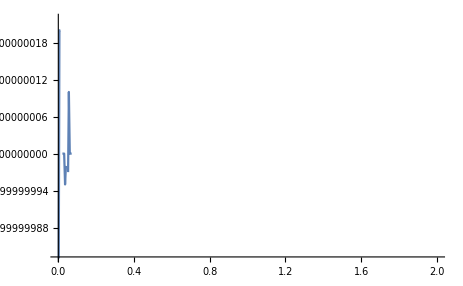

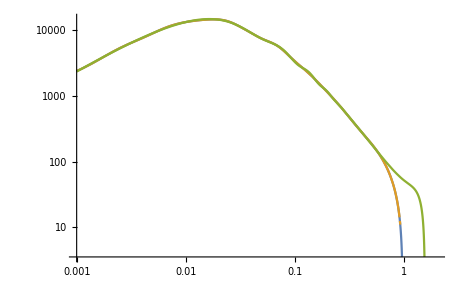

```mathematica
(*check that it is correct*)
Pintegerbabis[k_]=(coefnowig.matdiogotobabis).fbabistab/.henryparams;
Plot[Pinteger[k]-Pintegerbabis[k]+1,{k,0.001,2},PlotPoints->200]
LogLogPlot[{Pinteger[k],Pintegerbabis[k],Pirres[k]},{k,0.001,2}]
```

```mathematica
(*SetDirectory[NotebookDirectory[]];
Export["matdiogotobabis.csv",matdiogotobabis]*)
```

```mathematica
(*matbabistodiogo=Transpose[matdiogotobabis].Inverse[matdiogotobabis.Transpose[matdiogotobabis]]//Simplify;*)
```

## 1-loop power-spectrum - constructing tables of exponents and coefficients from kernels

```mathematica
ktab= {0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3(*,0.4,0.5,0.6,0.7,0.8,0.9,1.0*)};
```

```mathematica
subsp1loop={kmq-> √(q^2+k^2-2 k q ν),kpq-> √(q^2+k^2+2 k q ν)};
```

### Calculate P22

#### P22 tables

```mathematica
(*CTab22full has the form {n1,n2,n3,#} where n1 = Exponent[q^2], n2 = Exponent[(k-q)^2]*)
```

```mathematica
Clear[q,k,Tab22,CTab22full]
ker22 = (2F2s[q,k-q]F2s[q,k-q]/.{al->alfm,be->befm}/.mag[-q]->mag[q]/.{mag[q]->q,mag[k]->k,mag[-k]->k,mag[k1+k2]->k3,mag[k-q]->kmq,mag[k+q]->kpq}//Expand);
ker22list=(List@@ker22);
Tab22[k_] = Table[{Exponent[ker22list⟦i⟧,q^2],Exponent[ker22list⟦i⟧,kmq^2],0,ker22list⟦i⟧/.{q-> 1,kmq-> 1}},{i,1,Length[ker22list]}];
```

```mathematica
(*
This step combines coefficients that have the same exponents;
For P22, it doesn't change anything
*)

(*
pom=0;
For[i1=-3,i1≤3,i1++,For[i2=-3,i2≤3,i2++,For[i3=-3,i3≤3,i3++,If[Length[Cases[Tab22,{i1,i2,i3,_}]]>0,pom=pom+1]]]];
CTab22full=Table[{0,0,0,0},{i,1,pom}];
counter=1;
For[i1=-3,i1≤3,i1++,
For[i2=-3,i2≤3,i2++,
For[i3=-3,i3≤3,i3++,
If[Length[Cases[Tab22,{i1,i2,i3,_}]]>0,pom=Cases[Tab22,{i1,i2,i3,_}];
pom2=0;
For[i=1,i≤Length[pom],i++,pom2=pom2+pom⟦i,4⟧];
CTab22full⟦counter,1⟧=pom⟦1,1⟧;
CTab22full⟦counter,2⟧=pom⟦1,2⟧;
CTab22full⟦counter,3⟧=pom⟦1,3⟧;
CTab22full⟦counter,4⟧=pom2;
counter=counter+1;
]]]];*)
```

```mathematica
CTab22full[k_]=Sort[Tab22[k]];
```

```mathematica
(*Build tables with kernel exponents and coefficients*)
For[i=1,i≤Length[ktab],i++,
Export["P22ctabks/P22ctab_"<>ToString[10 ktab⟦i⟧//N]<>".csv",N[CTab22full[ktab⟦i⟧],40],"Table"]
]
```

#### Matrix multiplication

```mathematica
(*coefs=Rationalize[nlm["BestFitParameters"],10^-20];*)
```

```mathematica
jmat=Import["P22jmatbabis/jmatoutk_0.1.csv"];
jmattab = Table[ToExpression[StringReplace[jmat⟦i1,i2⟧,{"e"->"*10^","j"-> "ⅈ","("-> "",")"-> ""}]],{i1,1,Length[fbabisparamtab]},{i2,1,Length[fbabisparamtab]}];
```

```mathematica
(*jmattab//MatrixForm*)
```

```mathematica
(*Table[((matdiogotobabis.jmattab.Transpose[matdiogotobabis]).coefs)⟦i⟧Transpose[coefs]⟦i⟧,{i,1,20}]//MatrixForm*)
```

#### Numerical check

```mathematica
ker22simple=ker22/.{kmq-> √(q^2+k^2-2 k q ν)}//Simplify;
```

```mathematica
2π (1/(π)^(3/2))(NIntegrate[q^2 ker22simple Pirres[√(q^2+k^2-2 k q ν)/.k->0.01]Pirres[q]/.{k->0.01},{q,0,0.7},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->15,WorkingPrecision->15,Method->{"GlobalAdaptive","SymbolicProcessing"->0}])
```

212.000410832166

```mathematica
Sum[jmattab⟦i,j⟧c1⟦i⟧c1⟦j⟧,{i,1,Length[c1]},{j,1,Length[c1]}]
```

{360964. $Failed+$Failed {1} {{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},18,{0,0,38,0.+1.40126×10^-26 ⅈ}},14,1}+1
 |  |  |  |

```mathematica
2π (1/(π)^(3/2))(NIntegrate[q^2 ker22simple Plin[√(q^2+k^2-2 k q ν)/.{k->0.01}]Plin[q](*Boole[√(q^2+k^2-2 k q ν)> qir]*)/.{k->0.01},{q,10^-4,2},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->12])
```

211.981

#### Numerical check for general k

```mathematica
pbabis[q_]:=Sum[(fbabistab/.k-> q) ⟦i⟧,{i,1,Length[fbabistab]}];
```

```mathematica
2π (1/(π)^(3/2))(NIntegrate[q^2 ker22 pbabis[q]pbabis[kmq](*Boole[√(q^2+k^2-2 k q ν)> qir]*)/.{kmq-> √(q^2+k^2-2 k q ν)}/.{k->1},{q,0,∞},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->1])
```

1/(√π)2 NIntegrate[q^2 ker22 pbabis[q] pbabis[kmq]/.{kmq→√(q^2+k^2-2 k q ν)}/.{k→1},{q,0,∞},{ν,-1,1},Method→{GlobalAdaptive,SymbolicProcessing→0},PrecisionGoal→1]

### Calculate P13

#### P13 tables

```mathematica
ker13= (6F3s[q,-q,k]/.{al->alfm,be->befm}/.mag[-q]->mag[q]/.{mag[q]->q,mag[k]->k,mag[-k]->k,mag[k1+k2]->k3,mag[k-q]->kmq,mag[k+q]->kpq,mag[0]->0}//Expand);
(*ker13diogoUVν=Normal[Series[ker13diogo/.subsp1loop,{q,∞,2}]];
ker13diogoUV=Integrate[ker13diogoUVν,{ν,-1,1}]/2;*)
ker13UV=-(61 k^2)/(315 q^2);
ker13UVsafe=(ker13/.{kpq->kmq})-ker13UV;
ker13list[kk_]:=(List@@ker13UVsafe)/.{k->kk};
P13ctab[k_] := Table[{Exponent[ker13list[k]⟦i⟧,q^2],Exponent[ker13list[k]⟦i⟧,kmq^2],0,ker13list[k]⟦i⟧/.{q-> 1,kmq-> 1}},{i,1,Length[ker13list[k]]}];
```

```mathematica
For[i=1,i≤Length[kplotlist],i++,Export["P13ctabks/ctab13k_"<>ToString[10kplotlist⟦i⟧//N]<>"_.csv",(P13ctab[kplotlist⟦i⟧])//N,"Table"]]
```

#### Numerical Check of P13

```mathematica
jmat13=Import["P13jmatbabis/P13jmatoutk8.csv"];
jmattab13 = ParallelTable[ToExpression[StringReplace[jmat13[[i1]],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]],{i1,1,85}];
Plin[0.8]coefnowig.matdiogotobabis.jmattab13
Export["P13jmatfin/P13jmatfin_k_8.dat",Re[matdiogotobabis.jmattab13],"Table"];
```

```mathematica
ker13q=Integrate[ker13/.{kmq-> √(q^2+k^2-2 k q ν)},{ν,-1,1},Assumptions->{q>0,k>0}];
```

```mathematica
2π (1/(π)^(3/2))Plin[0.8](NIntegrate[q^2(ker13q pylinwig[q])/.k->0.8,{q,0.00001,15},Method->{"GlobalAdaptive"},PrecisionGoal->30,WorkingPrecision->40])
```

100.724 NIntegrate[q^2 (ker13q pylinwig[q])/.k→0.8,{q,0.00001,15},Method→{GlobalAdaptive},PrecisionGoal→30,WorkingPrecision→40]

```mathematica
Clear[P13mioFullFit]
P13mioFullFit[kk_]:=2π (1/(π)^(3/2))Plin[kk](NIntegrate[q^2(ker13q Plin[q])/.k->kk,{q,0.0001,3},Method->{"GlobalAdaptive"},PrecisionGoal->20,WorkingPrecision->30]);
```

```mathematica
P13mioFullFit[0.8]
```

100.724 NIntegrate[q^2 (ker13q Plin[q])/.k→0.8,{q,0.0001,3},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]

### Compute full P1-loop

```mathematica
wig = 0;
If[wig == 0,lenbabis = 41, lenbabis = 85];
If[wig == 0,p22filename = "P22jmatbabisnowig/jmatoutk_","P22jmatbabis/jmatoutk_"];
If[wig == 0,p13filename = "P13jmatbabisnowig/P13jmatoutk","P13jmatbabis/P13jmatoutk"];
If[wig == 0,p22out = "P22jmatfinnowig/P22jmatfin_k_","P22jmatfin/P22jmatfin_k_"];
If[wig == 0,p13out = "P13jmatfinnowig/P13jmatfin_k_","P13jmatfin/P13jmatfin_k_"];
If[wig == 0,diogotobabis = ToExpression[Import["matdiogotobabisnowig.csv"]],diogotobabis=ToExpression[Import["matdiogotobabis.csv"]]];
If[wig == 0,coefs = coefsnowig, coefs = coefswig];
If[wig == 0, pylin[q_]=Pinteger[q],pylin[q_] = coefs.diogotobabis.fbabistab];
```

```mathematica
Clear[jmat,jmattab,jmat13,jmattab13]
```

```mathematica
For[i = 1, i ≤ Length[ktab],i++,jmat[i]=Import[p22filename<>ToString[Round[10ktab⟦i⟧//N]]<>".csv"];
jmattab[i] = Table[ToExpression[StringReplace[jmat[i][[i1,i2]],{"e"->"*10^","j"-> "ⅈ","("-> "",")"-> ""}]],{i1,1,lenbabis},{i2,1,lenbabis}];
Export[p22out<>ToString[Round[10ktab⟦i⟧//N]]<>".dat",Re[diogotobabis.jmattab[i].Transpose[diogotobabis]],"Table"];]
```

```mathematica
For[i = 1, i ≤ Length[ktab],i++,jmat13[i]=Import[p13filename<>ToString[Round[10ktab⟦i⟧//N]]<>".csv"];
jmattab13[i] = ParallelTable[ToExpression[StringReplace[jmat13[i][[i1]],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]],{i1,1,lenbabis}];
Export[p13out<>ToString[Round[10ktab⟦i⟧//N]]<>".dat",Re[diogotobabis.jmattab13[i]],"Table"];]
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦5⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦9⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦13⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦17⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦21⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦6⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦10⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦14⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦18⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦22⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦7⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦11⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦15⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦19⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦23⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦24⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦27⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦30⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦33⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦36⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦39⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦25⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦28⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦31⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦34⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦37⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦40⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦26⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦29⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦32⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦35⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦38⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦41⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦5⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦9⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦13⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦17⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦21⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦6⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦10⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦14⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦18⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦22⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦7⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦11⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦15⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦19⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦23⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦24⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦27⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦30⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦33⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦36⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦39⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦25⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦28⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦31⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦34⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦37⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦40⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦26⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦29⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦32⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦35⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦38⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦41⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦5⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦9⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦13⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦17⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦21⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦6⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦10⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦14⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦18⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦22⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦7⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦11⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦15⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦19⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦23⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦24⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦27⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦30⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦33⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦36⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦39⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦25⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦28⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦31⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦34⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦37⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦40⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦26⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦29⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦32⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦35⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦38⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦41⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦5⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦9⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦13⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦17⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦21⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦6⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦10⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦14⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦18⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦22⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦7⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦11⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦15⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦19⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦23⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦24⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦27⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦30⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦33⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦36⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦39⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦25⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦28⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦31⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦34⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦37⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦40⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦26⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦29⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦32⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦35⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦38⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦41⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦5⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦9⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦13⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦17⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦21⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦1⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦6⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦10⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦14⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦18⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦22⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦7⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦11⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦15⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦19⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦23⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦24⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦27⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦30⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦33⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦36⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦39⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦25⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦28⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦31⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦34⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦37⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦40⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[$Failed⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification $Failed⟦26⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦29⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦32⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦35⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦38⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦41⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[$Failed⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[$Failed⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{-0.0000662896190099013087},{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[{-0.0000662896190099013087},{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 5 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 9 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 13 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 17 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 21 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 2 of {{-0.0000662896190099013087}} does not exist.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦5⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦9⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦13⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦17⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦21⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦2⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 6 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 10 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 14 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 18 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 22 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 3 of {{-0.0000662896190099013087}} does not exist.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦6⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦10⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦14⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦18⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦22⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

Part::partw: Part 7 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 11 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 15 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 19 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 23 of {{-0.0000662896190099013087}} does not exist.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦3⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of Part::partw will be suppressed during this calculation.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}].

Part::partw: Part 4 of {{-0.0000662896190099013087}} does not exist.

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦7⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦11⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦15⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦19⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦23⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partw: Part 24 of {{-0.0000662896190099013087}} does not exist.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}].

Part::partw: Part 27 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 30 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 33 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 36 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 39 of {{-0.0000662896190099013087}} does not exist.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦24⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}].

Part::partw: Part 25 of {{-0.0000662896190099013087}} does not exist.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦27⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦30⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦33⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦36⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦39⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}].

Part::partw: Part 28 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 31 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 34 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 37 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 40 of {{-0.0000662896190099013087}} does not exist.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦25⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}].

Part::partw: Part 26 of {{-0.0000662896190099013087}} does not exist.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦28⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦31⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦34⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦37⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦40⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 29 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 32 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 35 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 38 of {{-0.0000662896190099013087}} does not exist.

Part::partw: Part 41 of {{-0.0000662896190099013087}} does not exist.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}].

General::stop: Further output of Part::partw will be suppressed during this calculation.

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{-0.0000662896190099013087}}⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}].

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦26⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦29⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦32⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦35⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦38⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{-0.0000662896190099013087}}⟦41⟧,{e→*10^,j→*ⅈ,(→,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

Part::partw: Part 34 of {{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»} does not exist.

Part::partw: Part 36 of {{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»} does not exist.

Part::partw: Part 39 of {{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»} does not exist.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦34⟧,{e→*10^,j→*ⅈ,(→«2»,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦36⟧,{e→*10^,j→*ⅈ,(→«2»,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦39⟧,{e→*10^,j→*ⅈ,(→«2»,)→}].

ToExpression::notstrbox: StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦34⟧,{e→*10^,j→*ⅈ,(→«2»,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦36⟧,{e→*10^,j→*ⅈ,(→«2»,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦39⟧,{e→*10^,j→*ⅈ,(→«2»,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 35 of {{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»} does not exist.

Part::partw: Part 37 of {{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»} does not exist.

Part::partw: Part 40 of {{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»} does not exist.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦35⟧,{e→*10^,j→*ⅈ,(→«2»,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦37⟧,{e→*10^,j→*ⅈ,(→«2»,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦40⟧,{e→*10^,j→*ⅈ,(→«2»,)→}].

ToExpression::notstrbox: StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦35⟧,{e→*10^,j→*ⅈ,(→«2»,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦37⟧,{e→*10^,j→*ⅈ,(→«2»,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦40⟧,{e→*10^,j→*ⅈ,(→«2»,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 38 of {{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»} does not exist.

Part::partw: Part 41 of {{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦38⟧,{e→*10^,j→*ⅈ,(→«2»,)→}].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦41⟧,{e→*10^,j→*ⅈ,(→«2»,)→}].

General::stop: Further output of StringReplace::strse will be suppressed during this calculation.

ToExpression::notstrbox: StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦38⟧,{e→*10^,j→*ⅈ,(→«2»,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: StringReplace[{{(-5.303169520792104692e-04+0.000000000000000000e+00j)},{(5.556582071654149208e-04-3.779840469859831295e-04j)},«7»,{(-4.588746342327992660e-03-1.140248702979685357e-02j)},«23»}⟦41⟧,{e→*10^,j→*ⅈ,(→«2»,)→}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

```mathematica
p22tab = Table[{ktab⟦i⟧,coefs.(Import[p22out<>ToString[Round[10ktab⟦i⟧//N]]<>".dat","Table"]).coefs},{i,1,Length[ktab]}];
p13tab = Table[{ktab⟦i⟧,Plin[ktab⟦i⟧](coefs.(Import[p13out<>ToString[Round[10ktab⟦i⟧//N]]<>".dat","Table"]))⟦1⟧},{i,1,Length[ktab]}];
```

```mathematica
p1looptab = ParallelTable[{ktab⟦i⟧,p22tab⟦i,2⟧ + p13tab⟦i,2⟧},{i,1,Length[ktab]}]
```

{{0.01,21501.4 coefsnowig+coefsnowig.{{Re[{{1,,0,,0,,0,,0,,0,,0,,0,,0,,0,,0,,2717,0,,0,,0,,0,,0,,0,,0,,0,,0,,0,,kuv4^4/16}}]}}.coefsnowig},6,{0.3,1}}
 |  |  |  |

```mathematica
p22num[kk_]:=2π (1/(π)^(3/2))(NIntegrate[q^2 ker22simple Plin[kmq]Plin[q](*Boole[√(q^2+k^2-2 k q ν)> qir]*)/.{kmq-> √(q^2+k^2-2 k q ν)}/.{k->kk},{q,0.0001,3},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->12,WorkingPrecision->20]);
```

```mathematica
p13num[kk_]:=2π (1/(π)^(3/2))Plin[kk](NIntegrate[q^2(ker13q Plin[q])/.k->kk,{q,0.0001,3},Method->{"GlobalAdaptive"},PrecisionGoal->20,WorkingPrecision->30])
```

```mathematica
p22numint[kk_]:=2π (1/(π)^(3/2))(NIntegrate[q^2 ker22simple pylin[kmq]pylin[q](*Boole[√(q^2+k^2-2 k q ν)> qir]*)/.{kmq-> √(q^2+k^2-2 k q ν)}/.{k->kk},{q,0,∞},{ν,-1,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0},PrecisionGoal->12,WorkingPrecision->20])
```

```mathematica
p13numint[kk_]:=2π (1/(π)^(3/2))Plin[kk](NIntegrate[q^2(ker13q  pylin[q])/.k->kk,{q,0.000000001,10},Method->{"GlobalAdaptive"},PrecisionGoal->20,WorkingPrecision->30])
```

```mathematica
p22numinttab = Table[{ktab⟦i⟧,p22numint[ktab⟦i⟧]},{i,1,Length[ktab]}];//Quiet
```

```mathematica
p13numinttab = Table[{ktab⟦i⟧,p13numint[ktab⟦i⟧]},{i,1,Length[ktab]}];//Quiet
```

```mathematica
p1loopnuminttab = Table[{ktab⟦i⟧,p22numinttab⟦i,2⟧ + p13numinttab⟦i,2⟧},{i,1,Length[ktab]}]
```

{{0.01,213.91012958209965317+24261.7 NIntegrate[q^2 (ker13q pylin[q])/.k→0.01,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.02,2159.0430075421713845+25259.8 NIntegrate[q^2 (ker13q pylin[q])/.k→0.02,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.03,6660.2763662207256241+19999.4 NIntegrate[q^2 (ker13q pylin[q])/.k→0.03,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.04,12714.254631086581459+15015.1 NIntegrate[q^2 (ker13q pylin[q])/.k→0.04,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.05,19385.500578287145727+12043.2 NIntegrate[q^2 (ker13q pylin[q])/.k→0.05,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.1,53947.175098525714744+5160.24 NIntegrate[q^2 (ker13q pylin[q])/.k→0.1,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.2,89151.615791588791958+1805.69 NIntegrate[q^2 (ker13q pylin[q])/.k→0.2,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]},{0.3,99685.632699250742252+804.832 NIntegrate[q^2 (ker13q pylin[q])/.k→0.3,{q,1.×10^-9,10},Method→{GlobalAdaptive},PrecisionGoal→20,WorkingPrecision→30]}}

```mathematica
p1loopnumtab = Table[{ktab⟦i⟧,p22num[ktab⟦i⟧]+p13num[ktab⟦i⟧]},{i,1,Length[ktab]}];//Quiet
```

$Aborted

```mathematica
p1looprat = Table[{ktab⟦i⟧,Abs[(p1looptab⟦i,2⟧-p1loopnumtab⟦i,2⟧)/ p1loopnumtab⟦i,2⟧]},{i,1,Length[ktab]}]
p1loopplinrat = Table[{ktab⟦i⟧,Abs[(p1looptab⟦i,2⟧- p1loopnuminttab⟦i,2⟧)/ (p1loopnumtab⟦i,2⟧)]},{i,1,Length[ktab]}]
```

{{0.1,0.00107513},{0.2,0.00939089},{0.3,0.00631535},{0.4,0.0103051},{0.5,0.0063505},{0.6,0.000514346},{0.7,0.000720304},{0.8,0.0030615},{0.9,0.00720093},{1.,0.0098753}}

{{0.1,1.08574×10^-6},{0.2,7.26971×10^-7},{0.3,2.07973×10^-6},{0.4,2.36092×10^-6},{0.5,1.90878×10^-6},{0.6,9.09179×10^-8},{0.7,1.30721×10^-6},{0.8,3.96975×10^-7},{0.9,2.20066×10^-6},{1.,0.0000121315}}

```mathematica
p13tab
p13numinttab
```

{{0.1,-6310.72},{0.2,-13656.6},{0.3,-15892.7},{0.4,-17476.7},{0.5,-18084.7},{0.6,-18335.4},{0.7,-18357.9},{0.8,-18252.2},{0.9,-18073.3},{1.,-17847.6}}

{{0.1,-6310.72},{0.2,-13656.6},{0.3,-15892.7},{0.4,-17476.6},{0.5,-18084.6},{0.6,-18335.2},{0.7,-18357.6},{0.8,-18251.9},{0.9,-18072.8},{1.,-17847.1}}

```mathematica
p22tab
p22numinttab
```

{{0.1,34150.1},{0.2,53704.7},{0.3,59964.7},{0.4,60211.9},{0.5,59540.5},{0.6,58337.6},{0.7,56641.4},{0.8,54776.6},{0.9,52967.2},{1.,51303.5}}

{{0.1,34150.024999548236259},{0.2,53704.748250925306931},{0.3,59964.521862923277948},{0.4,60211.672853289899999},{0.5,59540.477986330367577},{0.6,58337.381935841270433},{0.7,56641.05236989071663},{0.8,54776.281687195753385},{0.9,52966.813828939286863},{1.,51303.407286827244421}}

```mathematica
p1loopnuminttab
p1looptab
p1loopnumtab
```

{{0.1,27839.3},{0.2,40048.2},{0.3,44071.9},{0.4,42735.1},{0.5,41455.9},{0.6,40002.2},{0.7,38283.4},{0.8,36524.4},{0.9,34894.},{1.,33456.4}}

{{0.1,27839.3},{0.2,40048.1},{0.3,44071.9},{0.4,42735.2},{0.5,41455.8},{0.6,40002.2},{0.7,38283.5},{0.8,36524.4},{0.9,34893.9},{1.,33455.9}}

{{0.1,27869.3},{0.2,40427.8},{0.3,43795.4},{0.4,43180.1},{0.5,41720.8},{0.6,39981.6},{0.7,38255.9},{0.8,36636.6},{0.9,35147.},{1.,33789.6}}

```mathematica
p22rat = Table[{ktab⟦i⟧,Abs[(p22tab⟦i,2⟧-p22numinttab⟦i,2⟧)/ p22numinttab⟦i,2⟧]},{i,1,Length[ktab]}]
p13rat = Table[{ktab⟦i⟧,Abs[(p13tab⟦i,2⟧-p13numinttab⟦i,2⟧)/ p13numinttab⟦i,2⟧]},{i,1,Length[ktab]}]
```

{{0.1,1.00421×10^-6},{0.2,1.13804×10^-7},{0.3,2.39593×10^-6},{0.4,3.26647×10^-6},{0.5,1.11279×10^-6},{0.6,3.46553×10^-6},{0.7,5.71784×10^-6},{0.8,6.62823×10^-6},{0.9,6.68185×10^-6},{1.,2.13606×10^-6}}

{{0.1,6.39381×10^-7},{0.2,1.70453×10^-6},{0.3,3.30899×10^-6},{0.4,5.42066×10^-6},{0.5,8.06722×10^-6},{0.6,0.0000112246},{0.7,0.0000149178},{0.8,0.0000190953},{0.9,0.0000238625},{1.,0.0000291087}}

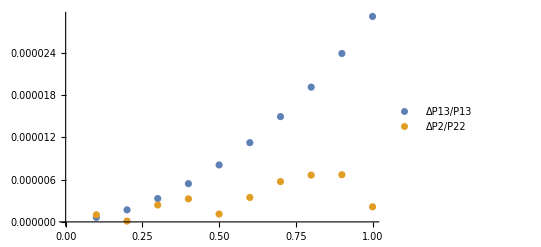

```mathematica
ListPlot[{p13rat,p22rat},PlotLegends->{"ΔP13/P13","ΔP2/P22"}]
```

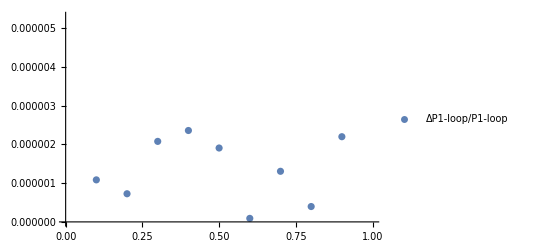

```mathematica
ListPlot[p1loopplinrat,PlotLegends->{"ΔP1-loop/P1-loop"}]
```

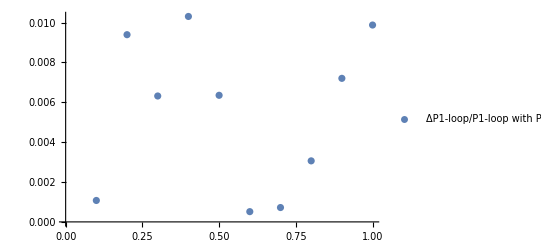

```mathematica
ListPlot[p1looprat,PlotLegends->{"ΔP1-loop/P1-loop with Plin"}]
```

## 1-loop bispectrum - constructing tables of exponents and coefficients from kernels

### Define relevant vectors and substitutions

```mathematica
Clear[k1vec,k2vec,qvec,k1,k2,k3,ϕs,q]
k1vec=k1{0,0,1};
ν2= (k3^2-k2^2-k1^2)/(2k1 k2);
k2vec=k2{0,√(1-ν2^2),ν2};
k3vec=-k1vec-k2vec;

qvec=q{Cos[ϕs] √(1-ν^2),Sin[ϕs] √(1-ν^2),ν};
k1mqvec=k1vec-qvec//Simplify;
k2pqvec=k2vec+qvec//Simplify;
k1pqvec=k1vec+qvec//Simplify;
k2mqvec=k2vec-qvec//Simplify;
k3pqvec=k3vec+qvec//Simplify;
k3mqvec=k3vec-qvec//Simplify;
```

```mathematica
subs={k1mq->√(k1mqvec.k1mqvec),k2pq->√(k2pqvec.k2pqvec),k1pq->√(k1pqvec.k1pqvec),k2mq->√(k2mqvec.k2mqvec),k3pq-> (k3pqvec.k3pqvec)^(1/2),k3mq-> (k3mqvec.k3mqvec)^(1/2)}//Simplify;
subs2k1={k1->1,k2->1,k3->1};
subs2k01=Rationalize[{k1->0.1,k2->0.1,k3->0.1}];
subs2k02=Rationalize[{k1->0.2,k2->0.2,k3->0.2}];
subs2k05=Rationalize[{k1->0.5,k2->0.5,k3->0.5}];
```

```mathematica
Clear[kuv1,kuv2,kuv3,kuv4,kpeak1,kpeak2,kpeak3,kpeak4]
babiscoef=coefnowig.(matdiogotobabis/.henryparams);
```

```mathematica
kuv1=0.069;
kuv2=0.0082;
kuv3=0.0013;
kuv4=0.0000135;
kpeak1=-0.034;
kpeak2=(*0.006*)-0.001;
kpeak3=(*0.000076*)-0.000076;
kpeak4=-0.0000156;kplotlist=kBins[30,0.005,0.5]
```

{0.005,0.00586051,0.00686912,0.00805131,0.00943696,0.0110611,0.0129647,0.015196,0.0178112,0.0208766,0.0244695,0.0286808,0.0336168,0.0394023,0.0461835,0.0541318,0.0634481,0.0743676,0.0871664,0.102168,0.119751,0.140361,0.164517,0.192831,0.226018,0.264916,0.310508,0.363948,0.426584,0.5}

### Import triangle points

```mathematica
ktabs = Import["Bisp_LightConeHector_cmass_ngc_mean.dat"];
ktabslen = Length[ktabs];
```

### B222

#### Build Ctab

```mathematica
Clear[k1,k2,k3,q,k2pq,k1mq]
ker222[k1_,k2_,k3_]=((((8F2s[q,k1-q]F2s[-q+k1,q+k2]F2s[k2+q,-q]/.{al->alfm,be->befm})/.mag[-q]->mag[q])/.{mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k1+k2]->k3,mag[k1-q]->k1mq,mag[-k1+q]->k1mq,mag[k2+q]->k2pq})//Expand);
ker222list[k1_,k2_,k3_]=(List@@ker222[k1,k2,k3]);
```

```mathematica
B222ctab[k1_,k2_,k3_] = Table[{Exponent[ker222list[k1,k2,k3]⟦i⟧,q^2],Exponent[ker222list[k1,k2,k3]⟦i⟧,k1mq^2],Exponent[ker222list[k1,k2,k3]⟦i⟧,k2pq^2],ker222list[k1,k2,k3]⟦i⟧/.{q-> 1,k1mq-> 1,k2pq-> 1}},{i,1,Length[ker222list[k1,k2,k3]]}];
```

```mathematica
B222ctabreduc[k1_,k2_,k3_]=Sort[B222ctab[k1,k2,k3]//.{a___,{p_,q_,r_,s1_},b___,{p_,q_,r_,s2_},c___}:>{a,{p,q,r,s1+s2},b,c}];
```

```mathematica
genb222ctab[k1_,k2_,k3_]:=Export["B222ctabks/B222ctab_"<>ToString[10k1//N]<>"_"<>ToString[10k2//N]<>"_"<>ToString[10k3//N]<>"_.csv",N[B222ctabreduc[Rationalize[k1],Rationalize[k2],Rationalize[k3]],80],"Table"];
```

```mathematica
For[i = 1, i ≤  Length[kplotlist], i++,genb222ctab[kplotlist⟦i⟧,kplotlist⟦i⟧,kplotlist⟦i⟧]]
```

```mathematica
(*ker222safe =Select[B222ctabreduc[1,1,1],#⟦1⟧<1 && #⟦2⟧ < 1&& #⟦3⟧ < 1&];*)
```

```mathematica
b222filelist=FileNames[All,"B222jmatbabisnowig_cython"]⟦2;;All⟧;
b222redfilelist=FileNames[All,"simple_redshiftspace_bispectrum/B222redjmatbabisnowig_cython"]⟦2;;All⟧;
```

```mathematica
cnc = SetPrecision[coefnowig.matdiogotobabis,20]
```

{-113.7533369829635177,-12924.388504931754142 ⅈ,12924.388504931754142 ⅈ,-9.6264835640629833335 ⅈ,9.6264835640629833335 ⅈ,-0.012514428633281858561,-0.012514428633281858561,0.13630568116311359006 ⅈ,-0.13630568116311359006 ⅈ,171.50874264381462808 ⅈ,-171.50874264381462808 ⅈ,-43.866766923231843123,-43.866766923231843123,-0.000024118957204489128489 ⅈ,0.000024118957204489128489 ⅈ,-4.8054890292968248004×10^-6,-4.8054890292968248004×10^-6,3.0085732097915718342,3.0085732097915718342,0.30399172188943418549 ⅈ,-0.30399172188943418549 ⅈ,2.669947823268796423×10^-8,2.669947823268796423×10^-8,-5.6267717673286732801×10^-11 ⅈ,5.6267717673286732801×10^-11 ⅈ,-0.44402418535665361121 ⅈ,0.44402418535665361121 ⅈ,0.0012533928500846921832,0.0012533928500846921832,1.3921394638221643763×10^-11 ⅈ,-1.3921394638221643763×10^-11 ⅈ,1.0550134229611709787×10^-15,1.0550134229611709787×10^-15}

```mathematica
test=Import["simple_redshiftspace_bispectrum/B222redjmatbabisnowig_cython/jmatoutk_0.05_0.05_0.05_.csv"];
jmatout = Table[test⟦2+i*33;;34+i*33,2;;-1⟧,{i,0,32}];
jmatoutfin2 = Table[ToExpression[StringReplace[ToString[jmatout⟦i,j,k⟧],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]],{i,1,Length[jmatout]},{j,1,Length[jmatout]},{k,1,Length[jmatout]}];
```

```mathematica
jmatoutfin2.cnc.cnc.cnc/(8π √π)
```

1828.47-1.79667×10^-12 ⅈ

```mathematica
computeB222[filename_]:=Module[{test,jmatout,jmatoutfin},
test=Import[filename];
jmatout = Table[test⟦2+i*33;;34+i*33,2;;-1⟧,{i,0,32}];
jmatoutfin = Table[ToExpression[StringReplace[ToString[jmatout⟦i,j,k⟧],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]],{i,1,Length[jmatout]},{j,1,Length[jmatout]},{k,1,Length[jmatout]}];
(jmatoutfin.cnc.cnc.cnc)/(8π √π)]
```

```mathematica
B222plotpoints=Table[{kplotlist⟦i⟧,computeB222[b222filelist⟦i⟧]},{i,1,Length[kplotlist]}];
B222redplotpoints=Table[{kplotlist⟦i⟧,computeB222[b222redfilelist⟦i⟧]},{i,1,Length[kplotlist]}];
```

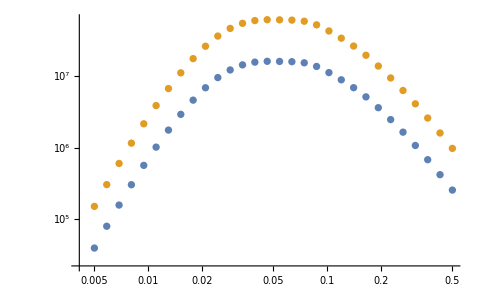

```mathematica
ListLogLogPlot[{Abs[B222plotpoints],Abs[B222redplotpoints]}]
```

```mathematica
Export["B222redplotpoints.dat",B222redplotpoints]
```

B222redplotpoints.dat

```mathematica
B222redctabs=FileNames[All,"simple_redshiftspace_bispectrum/B222redctabks"]⟦1;;-2⟧;
```

```mathematica
ker222red[filename_,plin_]:=Module[{ker222redfin,b222redctab,ksub},
b222redctab = Import[filename,"Table"];
ksub=ToExpression[StringSplit[filename,"_"]⟦-3⟧]/10;
ker222redfin = (Sum[b222redctab[[i,-1]] q^(-2b222redctab[[i,1]])k1mq^(-2 b222redctab[[i,2]])k2pq^(-2b222redctab[[i,3]]),{i,1,Length[b222redctab]}]plin[q]plin[k1mq]plin[k2pq])/.subs/.{k1-> ksub,k2-> ksub,k3-> ksub}]
```

```mathematica
B222numirres=Table[{kplotlist⟦i⟧,1/(2π)^3 NIntegrate[q^2 ker222red[B222redctabs⟦i⟧,Pirres],{q,0.0001,1},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,1789.3868774688769996},{0.00586051,4053.0687937454395803},{0.00686912,9034.828976165871072},{0.00805131,19767.178273372970896},{0.00943696,42313.994646127618972},{0.0110611,88288.22199631312752},{0.0129647,178758.7895717089173},{0.015196,349295.17028842016263},{0.0178112,654422.6546916755435},{0.0208766,1.1662488957805655757×10^6},{0.0244695,1.959006134099865233×10^6},{0.0286808,3.071043220479053826×10^6},{0.0336168,4.4535520300960449644×10^6},{0.0394023,5.9493996084718977832×10^6},{0.0461835,7.3675011648741766346×10^6},{0.0541318,8.6460261670657514551×10^6},{0.0634481,9.9377299110120269456×10^6},{0.0743676,1.1365965764790430334×10^7},{0.0871664,1.2497795026165656626×10^7},{0.102168,1.2509565807335301747×10^7},{0.119751,1.1583790530063858685×10^7},{0.140361,1.0581426038182165738×10^7},{0.164517,9.2658930335685290179×10^6},{0.192831,7.6538668620758839188×10^6},{0.226018,6.1450822505327483038×10^6},{0.264916,4.7191653369832292297×10^6},{0.310508,3.5007018201615245136×10^6},{0.363948,2.5154997398597687745×10^6},{0.426584,1.7576686667549150227×10^6},{0.5,1.1976988885342428193×10^6}}

```mathematica
B222numexact=Table[{kplotlist⟦i⟧,1/(2π)^3 NIntegrate[q^2 ker222red[B222redctabs⟦i⟧,Plin],{q,0.0001,1},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,1789.3864306713556878},{0.00586051,4053.0675825197833671},{0.00686912,9034.8256893991905093},{0.00805131,19767.169124145827061},{0.00943696,42313.968477258894258},{0.0110611,88288.14493773018714},{0.0129647,178758.36753208480185},{0.015196,349294.46765347298679},{0.0178112,654420.83318793784235},{0.0208766,1.1662448028900670602×10^6},{0.0244695,1.9589972820196687053×10^6},{0.0286808,3.0710262296624959756×10^6},{0.0336168,4.4535097248125686776×10^6},{0.0394023,5.9492530320044923918×10^6},{0.0461835,7.3670189497933559224×10^6},{0.0541318,8.6448464655122552052×10^6},{0.0634481,9.9359408205623118022×10^6},{0.0743676,1.1365339350221031666×10^7},{0.0871664,1.2500181037631583852×10^7},{0.102168,1.2508078598318261705×10^7},{0.119751,1.1570379363795772988×10^7},{0.140361,1.057805715655216332×10^7},{0.164517,9.2703534213672201169×10^6},{0.192831,7.6517435446851864908×10^6},{0.226018,6.1647695650364641511×10^6},{0.264916,4.7422885044180688256×10^6},{0.310508,3.5377310079379807581×10^6},{0.363948,2.5565830789812150003×10^6},{0.426584,1.7940524392138952272×10^6},{0.5,1.2266573715166117615×10^6}}

```mathematica
B222numfit=Table[{kplotlist⟦i⟧,1/(2π)^3 NIntegrate[q^2 ker222red[B222redctabs⟦i⟧,Pinteger],{q,0.001,0.6},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,1772.6866400461269881},{0.00586051,4017.9566209963155788},{0.00686912,9030.3558946209969528},{0.00805131,19979.695435942677554},{0.00943696,43065.682289598867972},{0.0110611,89668.366262061779926},{0.0129647,179607.03326886301146},{0.015196,345965.30649585871274},{0.0178112,641731.14893152375618},{0.0208766,1.1440786923579120249×10^6},{0.0244695,1.9406776796021206622×10^6},{0.0286808,3.0730151161851503343×10^6},{0.0336168,4.4655583391583066232×10^6},{0.0394023,5.9466168682865466771×10^6},{0.0461835,7.352326073924417248×10^6},{0.0541318,8.6428785817762064888×10^6},{0.0634481,9.9786431188554161185×10^6},{0.0743676,1.1408109987615855635×10^7},{0.0871664,1.2410223940620140242×10^7},{0.102168,1.2430907131640031353×10^7},{0.119751,1.1666657623690072059×10^7},{0.140361,1.0521499049938893183×10^7},{0.164517,9.1486976811926164152×10^6},{0.192831,7.6364131861769923935×10^6},{0.226018,6.1257956994775870317×10^6},{0.264916,4.7332588072997612923×10^6},{0.310508,3.5072874423526132531×10^6},{0.363948,2.4989292204200341309×10^6},{0.426584,1.7432595886278591408×10^6},{0.5,1.2017069717116507302×10^6}}

```mathematica
Export["B222numfit.dat",B222numfit];
Export["B222numexact.dat",B222numexact];
```

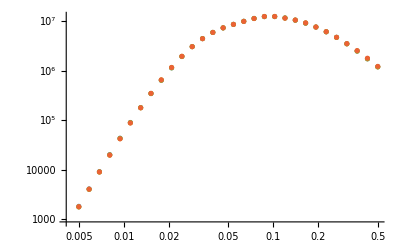

```mathematica
ListLogLogPlot[{Abs[B222redplotpoints],Abs[B222numirres],Abs[B222numfit],Abs[B222numexact]}]
```

```mathematica
Export["B222numirres.dat",B222numirres]
```

B222numirres.dat

```mathematica
1/(2 π)^3 NIntegrate[q^2(ker222[0.005,0.005,0.005]  Pirres[q]Pirres[k1mq]Pirres[k2pq]/.subs/.{k1-> 0.005,k2-> 0.005,k3-> 0.005}),{ϕs,0,2π},{ν,-1,1},{q,0.00001,5},PrecisionGoal->20,WorkingPrecision->20,MaxRecursion->15,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
```

$Aborted

```mathematica
B222Exact[k1sub_,k2sub_,k3sub_]:=Module[{ker222int,k1mqarg,k2pqarg},ker222int=Simplify[ker222[k1sub,k2sub,k3sub],Assumptions->{q>0,-1<ν<1,0<ϕs<2 π}];
k1mqarg=k1mq/. subs/. {k1->k1sub,k2->k2sub,k3->k3sub}//Simplify;
k2pqarg=k2pq/. subs/. {k1->k1sub,k2->k2sub,k3->k3sub}//Simplify;
1/(π)^(3/2) 10^-6 (NIntegrate[(q^2(ker222int/.{k1mq-> k1mqarg,k2pq-> k2pqarg})(Pirres[q] Pirres[k1mqarg] Pirres[k2pqarg])),{q,10^-4,1},{ν,-1,1},{ϕs,0,2 π},WorkingPrecision->10,Method->{Automatic,"SymbolicProcessing"->0}])];
```

```mathematica
b222res=B222Exact[0.1,0.1,0.1]
```

512.4284968

### B3211

```mathematica
ker3211=((6F3s[-q,q-k2,-k1]F2s[q,k2-q]/.{al->alfm,be->befm})/.{mag[0]->0,mag[-q]->mag[q],mag[-k1]->mag[k1],mag[-k2]->mag[k2]})/.{mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k1+k2]->k3,mag[-k1-k2]->k3,mag[k1-q]->k1mq,mag[k1+q]->k1pq,mag[-k1-q]->k1pq,mag[k2-q]->k2mq,mag[-k2+q]->k2mq,mag[k2+q]->k2pq,mag[k1+k2+q]->k3mq,mag[k1+k2-q]->k3pq,mag[-k1-k2+q]->k3pq}//Expand;
```

```mathematica
ker3211red12=0;
ker3211red23=0;
For[i=1,i≤Length[ker3211],i++,
pom1=D[ker3211⟦i⟧,k1pq]/.{k1pq->1,k2mq->1,k3pq->1,q->1,k1->1,k2->0.9,k3->0.7};
If[pom1==0,ker3211red23=ker3211red23+ker3211⟦i⟧,ker3211red12=ker3211red12+ker3211⟦i⟧];
];
```

```mathematica
ker3211final=(ker3211red12)+(((ker3211red23//Expand)/.{q->k2pqt,k2mq->qt,k3pq->k1mqt})/.{qt->q,k1mqt->k1pq,k2pqt->k2mq})//Expand;
```

```mathematica
ker3211final = ker3211final/.{k1pq-> k1mq, k2mq-> k2pq};
```

```mathematica
ker3211list=List@@ker3211final;
(*Monitor[For[i=1,i≤Length[ker3211],i++,
arr = -1/2 k3mq/ker3211⟦i⟧D[ker3211⟦i⟧,k3mq];
temp= ker3211⟦i⟧;
If[arr≠ 0,ker3211list⟦i⟧ = temp/.{k3mq->k1mq,k2pq-> q, q-> k2pq, k1mq-> weird }]],100.0*i/Length[ker3211]]*)
```

```mathematica
B3211ctab= Table[{Exponent[ker3211list⟦i⟧,q^2],Exponent[ker3211list⟦i⟧,k1mq^2],Exponent[ker3211list⟦i⟧,k2pq^2],ker3211list⟦i⟧/.{q-> 1,k1mq-> 1,k2pq-> 1}},{i,1,Length[ker3211list]}];
```

```mathematica
B3211ctabreduc=Sort[B3211ctab//.{a___,{p_,q_,r_,s1_},b___,{p_,q_,r_,s2_},c___}:>{a,{p,q,r,s1+s2},b,c}];
```

```mathematica
genb3211ctab[kk1_,kk2_,kk3_]:=Export["B3211ctabks/B3211ctab_"<>ToString[10kk1]<>"_"<>ToString[10kk2]<>"_"<>ToString[10kk3]<>"_.csv",N[B3211ctabreduc/.{k1-> Rationalize[kk1],k2-> Rationalize[kk2],k3-> Rationalize[kk3]},80],"Table"];
```

```mathematica
For[i = 1, i ≤  Length[kplotlist], i++,genb3211ctab[kplotlist⟦i⟧,kplotlist⟦i⟧,kplotlist⟦i⟧]]
```

```mathematica
b3211filelist=FileNames[All,"B3211jmatbabisnowig_cython"]⟦2;;-1⟧;
b3211redfilelist=FileNames[All,"simple_redshiftspace_bispectrum/B3211redjmatbabisnowig_cython"]⟦2;;-1⟧;
```

```mathematica
jmatout=Import["simple_redshiftspace_bispectrum/B3211redjmatbabisnowig_cython/jmatoutk_6.0_6.0_6.0_.csv"]⟦2;;-1,All⟧;
jmatoutfin = Table[SetPrecision[ToExpression[StringReplace[ToString[jmatout⟦i,j⟧],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]],50],{i,1,Length[jmatout]},{j,1,Length[jmatout]}];
```

```mathematica
jmatoutfin.cnc.cnc
```

67511.3-8.81181×10^-10 ⅈ

```mathematica
computeB3211[filename_]:=Module[{test,jmatout,jmatoutfin},
jmatout=Import[filename]⟦2;;-1,All⟧;
jmatoutfin = Table[SetPrecision[ToExpression[StringReplace[ToString[jmatout⟦i,j⟧],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]],50],{i,1,Length[jmatout]},{j,1,Length[jmatout]}];
(*10^-6*)(jmatoutfin.cnc.cnc)/(8π √π)]
```

```mathematica
B3211plotpoints=Table[{kplotlist⟦i⟧,6computeB3211[b3211filelist⟦i⟧]Plin[kplotlist⟦i⟧]},{i,1,Length[kplotlist]}];
```

```mathematica
B3211redplotpoints=Table[{kplotlist⟦i⟧,6computeB3211[b3211redfilelist⟦i⟧]Plin[kplotlist⟦i⟧]},{i,1,Length[kplotlist]}];
```

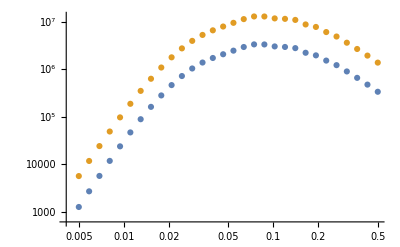

```mathematica
ListLogLogPlot[{Abs[B3211plotpoints],Abs[B3211redplotpoints]}]
```

```mathematica
Export["B3211plotpoints.dat",B3211plotpoints]
```

B3211plotpoints.dat

```mathematica
Export["B3211redplotpoints.dat",B3211redplotpoints]
```

B3211redplotpoints.dat

```mathematica
B3211redctabs=FileNames[All,"simple_redshiftspace_bispectrum/B3211redctabks"]⟦1;;-2⟧;
```

```mathematica
ker3211red[filename_,plin_]:=Module[{ker3211redfin,b3211redctab,ksub},
b3211redctab = Import[filename,"Table"];
ksub=ToExpression[StringSplit[filename,"_"]⟦-3⟧]/10;
ker3211redfin = (Sum[b3211redctab[[i,-1]] q^(-2b3211redctab[[i,1]])k1mq^(-2 b3211redctab[[i,2]])k2pq^(-2b3211redctab[[i,3]]),{i,1,Length[b3211redctab]}]plin[q]plin[k2pq])/.subs/.{k1-> ksub,k2-> ksub,k3-> ksub}]
```

```mathematica
B3211numirres=Table[{kplotlist⟦i⟧,6/(2π)^3 Plin[kplotlist⟦i⟧]NIntegrate[q^2 ker3211red[B3211redctabs⟦i⟧,Pirres],{q,0.0001,1},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,5545.32},{0.00586051,11585.9},{0.00686912,23883.6},{0.00805131,48425.},{0.00943696,96204.1},{0.0110611,186431.},{0.0129647,350402.},{0.015196,634751.},{0.0178112,1.09926×10^6},{0.0208766,1.80448×10^6},{0.0244695,2.78035×10^6},{0.0286808,3.99046×10^6},{0.0336168,5.32302×10^6},{0.0394023,6.65757×10^6},{0.0461835,8.01326×10^6},{0.0541318,9.58113×10^6},{0.0634481,1.14664×10^7},{0.0743676,1.30488×10^7},{0.0871664,1.30613×10^7},{0.102168,1.19001×10^7},{0.119751,1.16023×10^7},{0.140361,1.10954×10^7},{0.164517,8.89353×10^6},{0.192831,7.85205×10^6},{0.226018,6.12817×10^6},{0.264916,4.92354×10^6},{0.310508,3.65576×10^6},{0.363948,2.7091×10^6},{0.426584,1.9592×10^6},{0.5,1.38308×10^6}}

```mathematica
B3211numfit=Table[{kplotlist⟦i⟧,6/(2π)^3 Plin[kplotlist⟦i⟧]NIntegrate[q^2 ker3211red[B3211redctabs⟦i⟧,Pinteger],{q,0.001,0.6},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,5519.73},{0.00586051,11516.1},{0.00686912,23883.1},{0.00805131,48418.7},{0.00943696,96681.2},{0.0110611,196001.},{0.0129647,347249.},{0.015196,655704.},{0.0178112,1.07607×10^6},{0.0208766,1.80376×10^6},{0.0244695,2.75392×10^6},{0.0286808,4.04709×10^6},{0.0336168,5.34726×10^6},{0.0394023,6.72173×10^6},{0.0461835,8.0919×10^6},{0.0541318,9.47102×10^6},{0.0634481,1.15535×10^7},{0.0743676,1.30296×10^7},{0.0871664,1.29368×10^7},{0.102168,1.19103×10^7},{0.119751,1.06708×10^7},{0.140361,1.13891×10^7},{0.164517,8.5374×10^6},{0.192831,7.82624×10^6},{0.226018,6.14972×10^6},{0.264916,5.02367×10^6},{0.310508,3.65322×10^6},{0.363948,2.79228×10^6},{0.426584,1.96446×10^6},{0.5,1.36144×10^6}}

```mathematica
B3211numexact=Table[{kplotlist⟦i⟧,6/(2π)^3 Plin[kplotlist⟦i⟧]NIntegrate[q^2 ker3211red[B3211redctabs⟦i⟧,Plin],{q,0.001,0.6},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->15,WorkingPrecision->15,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,5452.02},{0.00586051,11427.3},{0.00686912,23620.8},{0.00805131,47991.6},{0.00943696,95517.1},{0.0110611,185511.},{0.0129647,348022.},{0.015196,633111.},{0.0178112,1.09358×10^6},{0.0208766,1.80003×10^6},{0.0244695,2.77421×10^6},{0.0286808,3.98687×10^6},{0.0336168,5.31697×10^6},{0.0394023,6.65138×10^6},{0.0461835,8.00615×10^6},{0.0541318,9.5698×10^6},{0.0634481,1.14638×10^7},{0.0743676,1.30384×10^7},{0.0871664,1.3056×10^7},{0.102168,1.18894×10^7},{0.119751,1.15641×10^7},{0.140361,1.11059×10^7},{0.164517,8.88885×10^6},{0.192831,7.85171×10^6},{0.226018,6.13497×10^6},{0.264916,4.94689×10^6},{0.310508,3.67583×10^6},{0.363948,2.7355×10^6},{0.426584,1.97504×10^6},{0.5,1.3713×10^6}}

```mathematica
Export["B3211numirres.dat",B3211numirres];
Export["B3211numexact.dat",B3211numexact];
Export["B3211numfit.dat",B3211numfit];
```

B3211numfit.dat

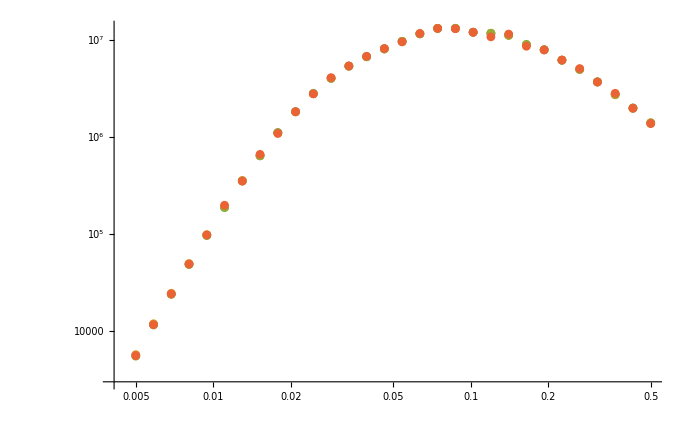

```mathematica
ListLogLogPlot[{B3211numirres,B3211redplotpoints,B3211numexact,B3211numfit}]
```

```mathematica
For[i = 1, i ≤ ktabslen, i++,
genb3211ctab[ktabs⟦i,1⟧,ktabs⟦i,2⟧,ktabs⟦i,3⟧]]
```

```mathematica
ker3211simp = Total[ker3211list]/.subs;
```

```mathematica
ker3211simpreduc = Simplify[(ker3211simp/.{k1->k1test,k2->k2test,k3->k3test}),Assumptions->{q>0}];
```

```mathematica
(1/(π)^(3/2))Plin[k1test]NIntegrate[q^2(ker3211simpreduc  Plin[k2pq/.subs/.{k1->k1test,k2->k2test,k3->k3test}]Plin[q]),{q,0.001,2},{ν,-1,1},{ϕs,0,2π},(*PrecisionGoal->10,*)AccuracyGoal->50,MaxRecursion->30,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
```

2.09107×10^7

### B411

```mathematica
Clear[ker411list,ker411listfin,ker411]
```

```mathematica
ker411=((12F4s[q,-q,k1,k2]/.{al->alfm,be->befm})/.{mag[0]->0,mag[-q]->mag[q]})/.{mag[q]->q,mag[k1]->k1,mag[k2]->k2,mag[k1+k2]->k3,mag[k1-q]->k1mq,mag[k1+q]->k1pq,mag[k2-q]->k2mq,mag[k2+q]->k2pq,mag[k1+k2+q]->k3mq,mag[k1+k2-q]->k3pq}//Expand;
```

```mathematica
(*Find UV limit of kernel*)

(*ker411lim=Normal[Series[ker411/.subs,{q,∞,2}]];
ker411limsimp=Simplify[ker411lim,{q>0,-1<ν<1}];
intker411lim=Integrate[ker411limsimp,{ϕs,0,2π},{ν,-1,1}]
ker411UV=intker411lim/(4π)//Simplify;*)
ker411UV = Expand[-1/(q^2 679140 k1^2 k2^2)(12024 k1^6+12024 k2^6-44518 k2^4 k3^2+20085 k2^2 k3^4+12409 k3^6-2 k1^4 (6012 k2^2+22259 k3^2)+k1^2 (-12024 k2^4+76684 k2^2 k3^2+20085 k3^4))];
```

```mathematica
ker411finqtok1mq=0;
ker411finqtok2pq=0;
ker411finq=0;
ker411finqsafe = 0;
For[i = 1, i ≤ Length[ker411],i++,
term = ker411⟦i⟧;
If[Exponent[ker411⟦i⟧,k3pq]≠ 0,If[Exponent[ker411⟦i⟧,k1mq]≠ 0,ker411finqtok1mq = ker411finqtok1mq + (term/.{k1pq-> k1mq,k3mq-> k3pq}),ker411finqtok2pq= ker411finqtok2pq + (term/.{k2mq-> k2pq,k3pq-> k3mq})],If[Exponent[ker411⟦i⟧,k3mq]≠ 0,If[Exponent[ker411⟦i⟧,k1pq]≠ 0,ker411finqtok1mq =ker411finqtok1mq+(term/.{k1pq-> k1mq,k3mq-> k3pq}),
ker411finqtok2pq = ker411finqtok2pq+(term/.{k2mq-> k2pq,k3pq-> k3mq})],ker411finq= ker411finq +  (term/.{k1pq-> k1mq,k2mq-> k2pq})]]];
ker411finqsafe = ker411finq - ker411UV(*-ker411IR*)//Expand;
ker411fin2 = ker411finqsafe + ker411finqtok1mq + ker411finqtok2pq;
```

```mathematica
B411ctab:= Module[{b411tabq,b411tabqtok1mq,b411tabqtok2pq,b411listq,b411listqtok1mq, b411listqtok2pq},
b411listq = List@@ker411finqsafe;
b411tabq = Table[{Exponent[b411listq⟦i⟧,q^2],1,Exponent[b411listq⟦i⟧,k1mq^2],0,Exponent[b411listq⟦i⟧,k2pq^2],0,b411listq⟦i⟧/.{q-> 1,k1mq-> 1,k2pq-> 1}},{i,1,Length[b411listq]}];
b411listqtok1mq = List@@ker411finqtok1mq;
b411tabqtok1mq = Table[{Exponent[b411listqtok1mq ⟦i⟧,q^2],0,Exponent[b411listqtok1mq ⟦i⟧,k1mq^2],1,Exponent[b411listqtok1mq ⟦i⟧,k3pq^2],0,b411listqtok1mq ⟦i⟧/.{q-> 1,k1mq-> 1,k3pq-> 1}},{i,1,Length[b411listqtok1mq ]}];
b411listqtok2pq = List@@ker411finqtok2pq;
b411tabqtok2pq = Table[{Exponent[b411listqtok2pq⟦i⟧,q^2],0,Exponent[b411listqtok2pq⟦i⟧,k3mq^2],0,Exponent[b411listqtok2pq⟦i⟧,k2pq^2],1,b411listqtok2pq⟦i⟧/.{q-> 1,k3mq-> 1,k2pq-> 1}},{i,1,Length[b411listqtok2pq]}];
Join[b411tabq,b411tabqtok1mq,b411tabqtok2pq]]
```

```mathematica
B411ctabreduc:=B411ctab//.{a___,{p_,q_,r_,s_,t_,u_,s1_},b___,{p_,q_,r_,s_,t_,u_,s2_},c___}:>{a,{p,q,r,s,t,u,s1+s2},b,c}
```

```mathematica
genb411ctab[kk1_,kk2_,kk3_]:=Export["B411ctabks/B411ctab_"<>ToString[10kk1]<>"_"<>ToString[10kk2]<>"_"<>ToString[10kk3]<>"_.csv",N[B411ctabreduc/.{k1-> Rationalize[kk1],k2-> Rationalize[kk2],k3-> Rationalize[kk3]},100],"Table"];
```

```mathematica
For[i = 1, i ≤  Length[kplotlist], i++,genb411ctab[kplotlist⟦i⟧,kplotlist⟦i⟧,kplotlist⟦i⟧]]
```

```mathematica
Dimensions[jmatout]
```

{34,1}

```mathematica
jmatout=Import["simple_redshiftspace_bispectrum/B411redjmatbabisnowig_cython/jmatoutk_0.27562_0.27562_0.27562_.csv"]⟦2;;-1⟧;
jmatoutfin = Table[SetPrecision[ToExpression[StringReplace[ToString[jmatout⟦i,1⟧],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]],30],{i,1,Length[jmatout]}];
```

```mathematica
SetPrecision[jmatoutfin.cnc,50]/(8 π √π)Plin[0.027562]^2 3
```

1.94×10^6+0. ⅈ

```mathematica
jmatout=Import["simple_redshiftspace_bispectrum/B411redjmatbabisnowig_cython/jmatoutk_0.05_0.05_0.05_.csv"]⟦2;;-1⟧;
jmatoutfin = Table[ToExpression[StringReplace[ToString[jmatout⟦i,1⟧],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]],{i,1,Length[jmatout]}];
(*10^-6*)SetPrecision[jmatoutfin.cnc,50]/(8 π √π)Plin[0.005]^2 3
```

5835.26

```mathematica
b411redfilelist=FileNames[All,"simple_redshiftspace_bispectrum/B411redjmatbabisnowig_cython"]⟦2;;-1⟧;
b411filelist=FileNames[All,"B411jmatbabisnowig_cython"]⟦2;;-1⟧;
```

```mathematica
computeB411[filename_]:=Module[{test,jmatout,jmatoutfin},
jmatout=Import[filename]⟦2;;-1⟧;
jmatoutfin = Table[ToExpression[StringReplace[ToString[jmatout⟦i,1⟧],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]],{i,1,Length[jmatout]}];
(*10^-6*)SetPrecision[jmatoutfin.cnc,80]/(8 π √π)]
```

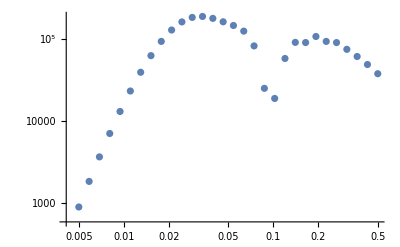

```mathematica
B411plotpoints=Table[{kplotlist⟦i⟧,3computeB411[b411filelist⟦i⟧]Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]},{i,1,Length[kplotlist]}];
ListLogLogPlot[Chop[Abs[B411plotpoints],10^-5]]
```

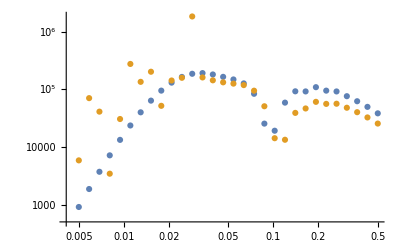

```mathematica
B411redplotpoints=Table[{kplotlist⟦i⟧,3computeB411[b411redfilelist⟦i⟧]Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]},{i,1,Length[kplotlist]}];
ListLogLogPlot[{Abs[B411plotpoints],Abs[B411redplotpoints]}]
```

```mathematica
b411redctab=Import["newCTab411_subk2.m"];
```

```mathematica
test=b411redctab/.f1-> 0.7770083924901465/.Thread[biases-> {1,1,1,1,0,0,0,0,0,0,0,0,0,0,0}]/.{y-> (k3^2-k1^2-k2^2)/(2 k1 k2)}/.{k1-> kplotlist⟦1⟧,k2->kplotlist⟦1⟧,k3-> kplotlist⟦1⟧}//N;
```

```mathematica
testint=Sum[test⟦i,-1⟧q^(-2b411redctab[[i,1]])k1mq^(-2b411redctab[[i,2]])k2pq^(-2b411redctab[[i,3]])If[D[test[[i,1]],ν]≠ 0,plin[q],If[D[test[[i,2]],ν]≠ 0,plin[k1mq],If[D[test[[i,3]],ν]≠ 0,plin[k2pq]]]]/.ν-> 0/.subs/.plin-> Plin,{i,1,Length[b411redctab]}];
```

```mathematica
3/(2π)^3 Plin[kplotlist⟦1⟧]Plin[kplotlist⟦1⟧]NIntegrate[q^2 testint/.subs/.{k1-> kplotlist⟦1⟧,k2-> kplotlist⟦1⟧,k3-> kplotlist⟦1⟧},{q,0.0001,2},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]
```

$Aborted

```mathematica
Clear[ker411red,b411redctab]
```

```mathematica
b411redfilelist[[12]]
```

simple_redshiftspace_bispectrum/B411redjmatbabisnowig_cython/jmatoutk_0.27562_0.27562_0.27562_.csv

```mathematica
ker411red[filename_,plin_]:=Module[{ker411redfin,b411redctab,ksub},
b411redctab = Import[filename,"Table"];
ksub=ToExpression[StringSplit[filename,"_"]⟦-3⟧]/10;
Print[ksub];
ker411redfin = Simplify[Sum[b411redctab[[i,7]] q^(-2b411redctab[[i,1]])k1mq^(-2b411redctab[[i,3]])k2pq^(-2b411redctab[[i,5]]) *If[b411redctab[[i,2]]≠ 0,plin[q],If[b411redctab[[i,4]]≠ 0,plin[k1mq],If[b411redctab[[i,6]]≠ 0,plin[k2pq]]]],{i,1,Length[b411redctab]}]/.subs/.{k1-> ksub,k2-> ksub,k3-> ksub}]
]
```

```mathematica
Export["B411plotpoints.dat",B411plotpoints]
Export["B411redplotpoints.dat",B411redplotpoints]
```

B411plotpoints.dat

B411redplotpoints.dat

```mathematica
B411redctabs⟦12⟧
```

simple_redshiftspace_bispectrum/B411redctabks/B411ctab_0.27562_0.27562_0.27562_.csv

```mathematica
3/(2π)^3 Plin[0.027562]Plin[0.027562]NIntegrate[q^2 ker411red[B411redctabs⟦12⟧,Pirres],{q,0.001,0.6},{ν,-1,1},{ϕs,0,2π},(*AccuracyGoal->15,WorkingPrecision->15,*)PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

0.027562

0.027562

-3.01799×10^9

```mathematica
B411redctabs=FileNames[All,"simple_redshiftspace_bispectrum/B411redctabks"]⟦1;;-2⟧;
```

```mathematica
B411numirres=Table[{kplotlist⟦i⟧,3/(2π)^3 Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]NIntegrate[q^2 ker411red[B411redctabs⟦i⟧,Plin],{q,0.0001,1},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->30,WorkingPrecision->30,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

$Aborted

```mathematica
B411numexact=Table[{kplotlist⟦i⟧,3/(2π)^3 Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]NIntegrate[q^2 ker411red[B411redctabs⟦i⟧,Plin],{q,0.0001,1},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,-5.27882×10^10},{0.00586051,-4.75675×10^10},{0.00686912,-4.21545×10^10},{0.00805131,-3.66076×10^10},{0.00943696,-3.106×10^10},{0.0110611,-2.56285×10^10},{0.0129647,-2.04763×10^10},{0.015196,-1.57379×10^10},{0.0178112,-1.15498×10^10},{0.0208766,-3.8421×10^10},{0.0244695,-5.31418×10^9},{0.0286808,-3.27976×10^9},{0.0336168,-3.98235×10^9},{0.0394023,-1.76455×10^10},{0.0461835,-7.83266×10^8},{0.0541318,-6.27619×10^8},{0.0634481,-7.55816×10^8},{0.0743676,-8.1628×10^9},{0.0871664,-1.188×10^9},{0.102168,-4.74768×10^8},{0.119751,-1.99408×10^9},{0.140361,-1.01821×10^9},{0.164517,-4.69874×10^8},{0.192831,-3.54918×10^8},{0.226018,-3.30195×10^8},{0.264916,-5.23923×10^8},{0.310508,-1.25417×10^9},{0.363948,-4.67776×10^8},{0.426584,-2.9564×10^8},{0.5,-2.53858×10^8}}

```mathematica
B411numfit=Table[{kplotlist⟦i⟧,3/(2π)^3 Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]NIntegrate[q^2 ker411red[B411redctabs⟦i⟧,Pinteger],{q,0.001,0.6},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

$Aborted

```mathematica
kplotlist
```

{0.005,0.00586051,0.00686912,0.00805131,0.00943696,0.0110611,0.0129647,0.015196,0.0178112,0.0208766,0.0244695,0.0286808,0.0336168,0.0394023,0.0461835,0.0541318,0.0634481,0.0743676,0.0871664,0.102168,0.119751,0.140361,0.164517,0.192831,0.226018,0.264916,0.310508,0.363948,0.426584,0.5}

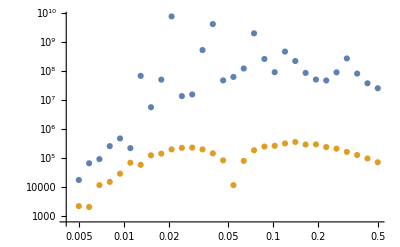

```mathematica
ListLogLogPlot[{Abs[B411numirres],Abs[B411redplotpoints]}]
```

```mathematica
B411numirres
```

{{0.005,-17133.5},{0.00586051,64276.8},{0.00686912,-89425.1},{0.00805131,-250896.},{0.00943696,-460998.},{0.0110611,-213727.},{0.0129647,-6.60708×10^7},{0.015196,-5.47091×10^6},{0.0178112,-4.89496×10^7},{0.0208766,-7.35684×10^9},{0.0244695,-1.32654×10^7},{0.0286808,-1.51195×10^7},{0.0336168,-5.12164×10^8},{0.0394023,-4.02227×10^9},{0.0461835,-4.61064×10^7},{0.0541318,-6.06656×10^7},{0.0634481,-1.18687×10^8},{0.0743676,-1.92881×10^9},{0.0871664,-2.52109×10^8},{0.102168,-8.84779×10^7},{0.119751,-4.53046×10^8},{0.140361,-2.14049×10^8},{0.164517,-8.36554×10^7},{0.192831,-4.94039×10^7},{0.226018,-4.59209×10^7},{0.264916,-8.75228×10^7},{0.310508,-2.63544×10^8},{0.363948,-7.92124×10^7},{0.426584,-3.6655×10^7},{0.5,-2.47162×10^7}}

```mathematica
ker411int=Simplify[(ker411-ker411UV)/.subs/.{k1-> k1test, k2->k2test, k3-> k3test},Assumptions->{q>0,-1<ν<1}];
```

```mathematica
1/(π)^(3/2)Plin[k3test]Plin[k2test]NIntegrate[qq^2(ker411int Pirres[qq]/.{q->qq}),{qq,0.001,3},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->10,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0},MaxRecursion->10]
```

4.88632×10^6

```mathematica
(*temp=FullSimplify[ker411int,Assumptions->{q>0,-1<ν<1,0<ϕs<2π}]*)
```

```mathematica
1/(π)^(3/2)Plin[k3test]Plin[k2test]NIntegrate[qq^2(ker411int Pinteger[qq]/.{q->qq}),{qq,0.00001,10},{ν,-1,1},{ϕs,0,2π},(*AccuracyGoal->10,*)WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0},MaxRecursion->20]
```

6.19172×10^6

### B3212

```mathematica
ker13= (6F3s[q,-q,k]/.{al->alfm,be->befm}/.mag[-q]->mag[q]/.{mag[q]->q,mag[k]->k,mag[-k]->k,mag[k1+k2]->k3,mag[k-q]->kmq,mag[k+q]->kpq,mag[0]->0}//Expand);
(*ker13diogoUVν=Normal[Series[ker13diogo/.subsp1loop,{q,∞,2}]];
ker13diogoUV=Integrate[ker13diogoUVν,{ν,-1,1}]/2;*)
ker13UV=-(61 k^2)/(315 q^2);
ker13UVsafe=(ker13/.{kpq->kmq})-ker13UV;
ker13list[kk_]:=(List@@ker13UVsafe)/.{k->kk};
P13ctab[k_] = Table[{Exponent[ker13list[k]⟦i⟧,q^2],Exponent[ker13list[k]⟦i⟧,kmq^2],0,ker13list[k]⟦i⟧/.{q-> 1,kmq-> 1}},{i,1,Length[ker13list]}];
```

```mathematica
For[i=1,i≤Length[kplotlist],i++,Export["P13ctabks/ctab13k_"<>ToString[10kplotlist⟦i⟧//N]<>"_.csv",(P13ctab[kplotlist⟦i⟧])//N,"Table"]]
```

```mathematica
b3212filelist=FileNames[All,"P13jmatbabisnowig_cython"];
b3212redfilelist=FileNames[All,"simple_redshiftspace_bispectrum/B3212redjmatbabisnowig_cython"]⟦2;;-1⟧;
```

```mathematica
jmat13=Import["P13jmatbabisnowig_cython/jmatoutk_0.05_0.05_0.05_.csv"]⟦2;;-1⟧;
jmattab13 = Table[ToExpression[StringReplace[ToString[jmat13⟦i1⟧],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]]/.j-> ⅈ,{i1,1,33}];
```

```mathematica
(cnc.jmattab13)[[1]]
```

0.0000482234+0. ⅈ

```mathematica
computeB3212[filename_]:=Module[{test,jmat13,jmattab13,ker3212part1},
jmat13=Import[filename]⟦2;;-1⟧;
jmattab13 = Table[ToExpression[StringReplace[ToString[jmat13⟦i1⟧],{"e"->"*10^","j"-> "*ⅈ","("-> "",")"-> ""}]]/.j-> ⅈ,{i1,1,33}];
(*10^-6*)((cnc.jmattab13)/(8π √π))[[1]]]
```

```mathematica
ker3212part1[k1_,k2_,k3_] = F2s[k1,k2]/.{al->alfm,be->befm}/.magreps;
```

```mathematica
B3212plotpoints=Table[{kplotlist⟦i⟧,6computeB3212[b3212filelist⟦i⟧]Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]ker3212part1[kplotlist⟦i⟧,kplotlist⟦i⟧,kplotlist⟦i⟧]},{i,1,Length[kplotlist]}];
```

```mathematica
B3212redplotpoints=Table[{kplotlist⟦i⟧,6computeB3212[b3212redfilelist⟦i⟧]Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]ker3212part1[kplotlist⟦i⟧,kplotlist⟦i⟧,kplotlist⟦i⟧]},{i,1,Length[kplotlist]}];
```

```mathematica
Export["B3212plotpoints.dat",B3212plotpoints]
```

B3212plotpoints.dat

```mathematica
Export["B3212redplotpoints.dat",B3212redplotpoints]
```

B3212redplotpoints.dat

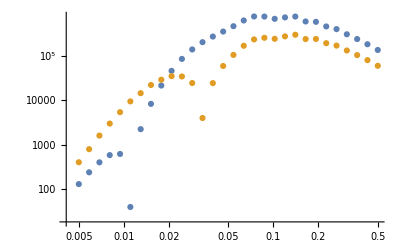

```mathematica
ListLogLogPlot[{Abs[B3212plotpoints],Abs[B3212redplotpoints]}]
```

```mathematica
B3212redctabs=FileNames[All,"simple_redshiftspace_bispectrum/B3212redctabks"]⟦1;;-2⟧;
```

```mathematica
ker3212red[filename_,plin_]:=Module[{ker3212redfin,b3212redctab,ksub},
b3212redctab = Import[filename,"Table"];
ksub=ToExpression[StringSplit[filename,"_"]⟦-3⟧]/10;
ker3212redfin = (Sum[b3212redctab[[i,-1]] q^(-2b3212redctab[[i,1]])k1mq^(-2 b3212redctab[[i,2]])k2pq^(-2b3212redctab[[i,3]]),{i,1,Length[b3212redctab]}]plin[q])/.subs/.{k1-> ksub,k2-> ksub,k3-> ksub}]
```

```mathematica
B3212numirres=Table[{kplotlist⟦i⟧,6/(2π)^3 Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]NIntegrate[q^2 ker3212red[B3212redctabs⟦i⟧,Pirres],{q,0.0001,1},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,1428.5},{0.00586051,2920.74},{0.00686912,5595.47},{0.00805131,10588.6},{0.00943696,17678.5},{0.0110611,32089.2},{0.0129647,52867.5},{0.015196,77285.},{0.0178112,105650.},{0.0208766,123954.},{0.0244695,121921.},{0.0286808,85954.5},{0.0336168,14908.7},{0.0394023,-84041.9},{0.0461835,-206273.},{0.0541318,-367791.},{0.0634481,-591847.},{0.0743676,-822567.},{0.0871664,-894557.},{0.102168,-850037.},{0.119751,-964067.},{0.140361,-1.04793×10^6},{0.164517,-837848.},{0.192831,-841448.},{0.226018,-674811.},{0.264916,-595893.},{0.310508,-461510.},{0.363948,-362034.},{0.426584,-277623.},{0.5,-206438.}}

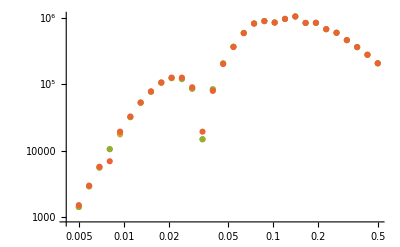

```mathematica
ListLogLogPlot[{Abs[B3212redctabs],Abs[B3212numirres],Abs[B3212numexact],Abs[B3212numfit]}]
```

```mathematica
Export["B3212numexact.dat",B3212numexact];
Export["B3212numfit.dat",B3212numfit];
Export["B3212numirres.dat",B3212numirres];
```

```mathematica
B3212numexact=Table[{kplotlist⟦i⟧,6/(2π)^3 Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]NIntegrate[q^2 ker3212red[B3212redctabs⟦i⟧,Plin],{q,0.0001,1},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,1428.48},{0.00586051,2921.03},{0.00686912,5595.22},{0.00805131,10588.7},{0.00943696,19041.3},{0.0110611,32084.8},{0.0129647,52872.1},{0.015196,77280.8},{0.0178112,105658.},{0.0208766,123955.},{0.0244695,119732.},{0.0286808,85958.1},{0.0336168,14918.7},{0.0394023,-84024.3},{0.0461835,-206244.},{0.0541318,-367738.},{0.0634481,-591752.},{0.0743676,-822413.},{0.0871664,-894380.},{0.102168,-849991.},{0.119751,-963811.},{0.140361,-1.04757×10^6},{0.164517,-837505.},{0.192831,-841048.},{0.226018,-674450.},{0.264916,-595556.},{0.310508,-461252.},{0.363948,-361853.},{0.426584,-277516.},{0.5,-206391.}}

```mathematica
B3212numfit=Table[{kplotlist⟦i⟧,6/(2π)^3 Plin[kplotlist⟦i⟧]Plin[kplotlist⟦i⟧]NIntegrate[q^2 ker3212red[B3212redctabs⟦i⟧,Pinteger],{q,0.001,0.6},{ν,-1,1},{ϕs,0,2π},AccuracyGoal->20,WorkingPrecision->20,Method->{Automatic,"SymbolicProcessing"->0}]},{i,1,Length[kplotlist]}]
```

{{0.005,1524.52},{0.00586051,2995.66},{0.00686912,5764.03},{0.00805131,6964.13},{0.00943696,19418.6},{0.0110611,32779.8},{0.0129647,53266.2},{0.015196,78302.5},{0.0178112,106618.},{0.0208766,126181.},{0.0244695,126076.},{0.0286808,90253.6},{0.0336168,19396.7},{0.0394023,-79589.5},{0.0461835,-201753.},{0.0541318,-362987.},{0.0634481,-586832.},{0.0743676,-817985.},{0.0871664,-891101.},{0.102168,-847530.},{0.119751,-961566.},{0.140361,-1.04669×10^6},{0.164517,-836875.},{0.192831,-841026.},{0.226018,-675137.},{0.264916,-596467.},{0.310508,-461923.},{0.363948,-363211.},{0.426584,-278771.},{0.5,-207564.}}

```mathematica
ker13q=Integrate[ker13/.{kmq-> √(q^2+k^2-2 k q ν)},{ν,-1,1},Assumptions->{q>0,k>0}];
```

### Redshiftspace Full 1loop bispectrum

```mathematica
bredtot =B222redplotpoints⟦All,2⟧+B3211redplotpoints⟦All,2⟧+B3212redplotpoints⟦All,2⟧+B411redplotpoints⟦All,2⟧;
```

```mathematica
bredtotplot=Table[{B222redplotpoints⟦i,1⟧,bredtot⟦i⟧},{i,1,Length[kplotlist]}];
```

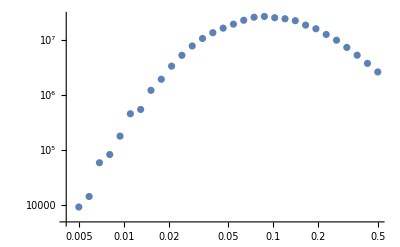

```mathematica
ListLogLogPlot[Abs[bredtotplot]]
```

```mathematica
bredtotplot[[18]]
```

{0.0743676,2.53653×10^7+1.18645×10^-9 ⅈ}

```mathematica
Import["DMreedbispectrum.mx"]/.{f1-> 0.7770083924901465}
```

{{{0.01,0.01,0.01},-2.46529×10^6},{{0.08,0.08,0.01},3.39698×10^9},{{0.08,0.08,0.08},-2.0599×10^6},{{0.15,0.08,0.08},-3.76891×10^7},{{0.15,0.15,0.01},5.99199×10^10},{{0.15,0.15,0.08},6.27997×10^6},{{0.15,0.15,0.15},4.19643×10^6},{{0.22,0.15,0.08},-5.73618×10^6},{{0.22,0.15,0.15},2.38663×10^6},{{0.22,0.22,0.01},2.88122×10^11},{{0.22,0.22,0.08},3.9214×10^7},{{0.22,0.22,0.15},4.6511×10^6},{{0.22,0.22,0.22},4.32291×10^6},{{0.29,0.15,0.15},1.06021×10^6},{{0.29,0.22,0.08},5.70593×10^7},{{0.29,0.22,0.15},4.69909×10^6},{{0.29,0.22,0.22},3.79006×10^6},{{0.29,0.29,0.01},9.2007×10^11},{{0.29,0.29,0.08},1.18779×10^8},{{0.29,0.29,0.15},4.93821×10^6},{{0.29,0.29,0.22},3.15685×10^6},{{0.29,0.29,0.29},2.65085×10^6}}

## Functions to compare with Maple/Python code

### Numerical integrals using Feynman parameters

```mathematica
BubN[n1_,n2_,Q_,M1_,M2_]:=Gamma[n1+n2-3/2]/(Gamma[n1]Gamma[n2])NIntegrate[(x^(n1-1)(1-x)^(n2-1))/(√(x(1-x)Q+x M1+(1-x) M2))^(2n1+2n2-3),{x,0,1},PrecisionGoal->30,WorkingPrecision->30,AccuracyGoal->30,Method->{"GlobalAdaptive","SymbolicProcessing"->0}];
```

```mathematica
TrN[n1_,n2_,n3_,Q1_,Q2_,Q3_,M1_,M2_,M3_]:=Module[{x1,x2,x3,l1,l2},(Gamma[n1+n2+n3-3/2]/(Gamma[n1]Gamma[n2]Gamma[n3]))NIntegrate[(x1^(n1-1)x2^(n2-1) x3^(n3-1)(1-x1))/(√(x1 x2 Q1+x2 x3 Q2+x3 x1 Q3+ x1 M1 + x2 M2 + x3 M3))^(2n1+2n2+2n3-3)/.{x1->l1,x2->l2(1-l1),x3->(1-l2)(1-l1)},{l1,0,1},{l2,0,1},PrecisionGoal->10,WorkingPrecision->15,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]];
```

### Numerical integrals using momentum integrals

```mathematica
BubNk[n1_,n2_,k1_,M1_,M2_]:=Module[{k1vec,qvec,k1mqvec},
k1vec=k1{0,0,1};
qvec=q{√(1-ν^2),0,ν};
k1mqvec=k1vec-qvec//Simplify;
((2π)/π^(3/2))NIntegrate[q^2/((k1mqvec.k1mqvec+M1)^n1(qvec.qvec+M2)^n2),{q,0,∞},{ν,-1,1},PrecisionGoal->10,WorkingPrecision->20(*,Method->"LocalAdaptive"*)]
];

BubNkgen[n1_,d1_,n2_,d2_,k1_,M1_,M2_]:=Module[{k1vec,qvec,k1mqvec},
k1vec=k1{0,0,1};
qvec=q{√(1-ν^2),0,ν};
k1mqvec=k1vec-qvec//Simplify;
((2π)/π^(3/2))NIntegrate[(q^2   (k1mqvec.k1mqvec)^n1(qvec.qvec)^n2)/((k1mqvec.k1mqvec+M1)^d1(qvec.qvec+M2)^d2),{q,0,∞},{ν,-1,1},PrecisionGoal->10,WorkingPrecision->20,Method->"GlobalAdaptive"]
];

BubNkgen2[n1_,d1_,n2_,d2_,k1_,M1_,M2_]:=Module[{k1vec,qvec,k1mqvec},
k1vec=k1{0,0,1};
qvec=q{√(1-ν^2),0,ν};
k1mqvec=k1vec-qvec//Simplify;

((2π)/π^(3/2))NIntegrate[(q^2   (k1mqvec.k1mqvec)^n1(qvec.qvec)^n2)/((k1mqvec.k1mqvec+M1)^d1(qvec.qvec+M2)^d2),{q,0,∞},{ν,-1,1},PrecisionGoal->10,Method->"GlobalAdaptive"]
];


Clear[intν,d1,d2,n1,n2];
intν[q_,n1_,d1_,n2_,d2_,k1_,M1_,M2_,ν_]:=(*((2π)/π^(3/2))q^2  Integrate[((k1mqvec.k1mqvec)^n1(qvec.qvec)^n2 )/((k1mqvec.k1mqvec+M1)^d1(qvec.qvec+M2)^d2),{ν,-1,1}];*)-(1/(k1 M1 √π))q (q^2)^n2 (M2+q^2)^-d2 (k1^2+q^2-2 k1 q ν)^(1+n1) (k1^2+M1+q^2-2 k1 q ν)^(1-d1) (1/(1+n1))Hypergeometric2F1[1,2-d1+n1,2+n1,-((k1^2+q^2-2 k1 q ν)/M1)];
(*BubNkgen3[n1_,d1_,n2_,d2_,k1_,M1_,M2_]:=Module[{k1vec,qvec,k1mqvec,q},
k1vec=k1{0,0,1};
qvec=q{√(1-ν^2),0,ν};
k1mqvec=k1vec-qvec//Simplify;

intνval=intν[q,n1,d1,n2,d2,k1,M1,M2,1]-intν[q,n1,d1,n2,d2,k1,M1,M2,-1]//Simplify;
NIntegrate[intνval,{q,0,∞},PrecisionGoal->10,Method->"GlobalAdaptive"]
];*)
```

```mathematica
TrNk[n1_,n2_,n3_,k1_,k2_,k3_,M1_,M2_,M3_]:=Module[{k1vec,k2vec,qvec,k1mqvec,k2pqvec,ν2},
k1vec=k1{0,0,1};
ν2=(1/(2k1 k2))(k3^2-k2^2-k1^2);
k2vec=k2{0,√(1-ν2^2),ν2};
qvec=q{Cos[ϕ]√(1-ν^2),Sin[ϕ]√(1-ν^2),ν};
k1mqvec=k1vec-qvec//Simplify;
k2pqvec=k2vec+qvec//Simplify;
(1/π^(3/2))NIntegrate[q^2/((k1mqvec.k1mqvec+M1)^n1(qvec.qvec+M2)^n2(k2pqvec.k2pqvec+M3)^n3),{q,0,10000},{ν,-1,1},{ϕ,0,2π},PrecisionGoal->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
];

TrNkgen[n1_,n2_,n3_,d1_,d2_,d3_,k1_,k2_,k3_,M1_,M2_,M3_]:=Module[{k1vec,k2vec,qvec,k1mqvec,k2pqvec,ν2},
k1vec=k1{0,0,1};
ν2=(1/(2k1 k2))(k3^2-k2^2-k1^2);
k2vec=k2{0,√(1-ν2^2),ν2};
qvec=q{Cos[ϕ]√(1-ν^2),Sin[ϕ]√(1-ν^2),ν};
k1mqvec=k1vec-qvec//Simplify;
k2pqvec=k2vec+qvec//Simplify;
(1/π^(3/2))NIntegrate[q^2 (k1mqvec.k1mqvec)^n1(qvec.qvec)^n2(k2pqvec.k2pqvec)^n3/((k1mqvec.k1mqvec+M1)^d1(qvec.qvec+M2)^d2(k2pqvec.k2pqvec+M3)^d3),{q,0,1000},{ν,-1,1},{ϕ,0,2π},PrecisionGoal->30,Method->{"GlobalAdaptive","SymbolicProcessing"->0}]
];
```

### Exact integral for tadpole

```mathematica
A=Simplify[-ⅈ π^(d/2) Exp[ⅈ d π/4] (-ⅈ m2)^(1/2(-2+d))Gamma[1-d/2]];
Asimple=FullSimplify[A/.{d->3},Assumptions->Im[m2]>0];
Asimpler=-2 √m2 π^2;
```

```mathematica
(*test that we get exact integral value by differentiating wrt m2*)
```

```mathematica
derivA=-D[Asimpler,m2]//Simplify;
NumA[a_,M_]:=4π NIntegrate[q^2/((q^2+M)^a),{q,0,∞}];
```